```mathematica
subs={α->x √2,β->-x √2}/.x->1
```

```mathematica
subs={α->3 x √2,β->-x √2}/.x->1/√2
```

```mathematica
θ=N[(4 β)/(α+β)/.subs]
```

```mathematica
z=N[(16+α^2+2 α β-3 β^2)/(α^2-β^2)/.subs]
```

```mathematica
N[(2- θ)/z]
```

```mathematica
Simplify[(4 β (-α+β))/(16+α^2+2 α β-3 β^2)/.subs]
```

```mathematica
Solve[-(2 x^2)/(-2+x^2)==2,x]
```

```mathematica
T[μ_]:=-(μ^2-12)/(8 π μ)
```

```mathematica
wp=MachinePrecision;
$MinPrecision=wp;
type="Real64";
Ctype="Complex128";
itype="Integer32";
itype="Integer64";
```

```mathematica
wp=34;
$MinPrecision=wp;
type="Real128";
itype="Integer64";
Ctype="Complex256";
```

```mathematica
ClearMemory:=Module[{},Unprotect[In,Out];Clear[In,Out];Protect[In,Out];ClearSystemCache[];];
```

```mathematica
ClearMemory[];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/aristos/Documents/Notes/AdS:CMT/JJCorrelator/EMDLattice/NumericsPatch

```mathematica
SetDirectory[HomeDirectory[]<>"/Temporary/CamHome/private/CPPCode/Lattice/LatticeNumerics"];
```

## Fdiff-Spectral

```mathematica
order=6;
order2=6;
mid=80/100;
NpT1=300;
NpT2=30;
Nx=35;
rgrid1=N[mid*1/2(1+Cos[π(1- Range[0,1,1/(NpT1-1)])]),wp];
rgrid1=N[Range[0,mid,mid/(NpT1-1)],wp];
rgrid2=N[Range[mid,1,(1-mid)/(NpT2-1)],wp];
rgrid2=N[mid+(1-mid)*1/2(1+Cos[π(1- Range[0,1,1/(NpT2-1)])]),wp];
rgrid=Join[rgrid1,rgrid2];
xgrid=N[Range[0,1,1/Nx],wp];
NpTT=Length[rgrid];
d101=NDSolve`FiniteDifferenceDerivative[Derivative[1],{rgrid1},DifferenceOrder->{order},
PeriodicInterpolation->{False}];
d201=NDSolve`FiniteDifferenceDerivative[Derivative[2],{rgrid1},DifferenceOrder->{order}];
d102=NDSolve`FiniteDifferenceDerivative[Derivative[1],{rgrid2},DifferenceOrder->"Pseudospectral",
PeriodicInterpolation->{False}];
d202=NDSolve`FiniteDifferenceDerivative[Derivative[2],{rgrid2},DifferenceOrder->"Pseudospectral",PeriodicInterpolation->{False}];
d01=NDSolve`FiniteDifferenceDerivative[Derivative[1],{xgrid},DifferenceOrder->"Pseudospectral",
PeriodicInterpolation->{True}];
d02=NDSolve`FiniteDifferenceDerivative[Derivative[2],{xgrid},DifferenceOrder->"Pseudospectral",PeriodicInterpolation->{True}];
RadialId1=N[IdentityMatrix[NpT1],wp];
RadialId2=N[IdentityMatrix[NpT2],wp];
SpatialId=N[IdentityMatrix[Nx],wp];
diffd101=Transpose[Map[d101,RadialId1]];
diffd201=Transpose[Map[d201,RadialId1]];
diffd102=Transpose[Map[d102,RadialId2]];
diffd202=Transpose[Map[d202,RadialId2]];
diffd01=Transpose[Map[d01,SpatialId]];
diffd02=Transpose[Map[d02,SpatialId]];
Diffd10=Partition[Join[Flatten[PadRight[#,NpTT]&/@diffd101],Flatten[PadLeft[#,NpTT]&/@diffd102]],NpTT];
Diffd20=Partition[Join[Flatten[PadRight[#,NpTT]&/@diffd201],Flatten[PadLeft[#,NpTT]&/@diffd202]],NpTT];
d[1,0][A_]:=Diffd10.A;d[2,0][A_]:=Diffd20.A;d[1,1][A_]:=Diffd10.A.Transpose[diffd01];d[0,1][A_]:=A.Transpose[diffd01];d[0,2][A_]:=A.Transpose[diffd02];
```

```mathematica
BinaryWrite["cheby_d1.dat",SetPrecision[Flatten[Diffd10],wp],type];Close["cheby_d1.dat"];
BinaryWrite["cheby_d2.dat",SetPrecision[Flatten[Diffd20],wp],type];Close["cheby_d2.dat"];
BinaryWrite["fourier_d1.dat",SetPrecision[Flatten[diffd01],wp],type];Close["fourier_d1.dat"];
BinaryWrite["fourier_d2.dat",SetPrecision[Flatten[diffd02],wp],type];Close["fourier_d2.dat"];
BinaryWrite["rgrid.dat",SetPrecision[Flatten[rgrid],wp],type];Close["rgrid.dat"];
BinaryWrite["xgrid.dat",SetPrecision[Flatten[xgrid[[1;;-2]]],wp],type];Close["xgrid.dat"];
BinaryWrite["Rdimensions.dat",{NpT1,NpT2},itype];Close["Rdimensions.dat"];
BinaryWrite["ROrders.dat",{order+2,NpT2},itype];Close["ROrders.dat"];
BinaryWrite["Xdimensions.dat",{Nx},itype];Close["Xdimensions.dat"];
```

## Fdiff-Fdiff-Fdiff

```mathematica
order=6;
order2=6;
mid1=92/100;
mid2=98/100;
NpT1=300;
NpT2=50;
NpT3=50;
Nx=30;
rgrid1=N[Range[0,mid1,mid1/(NpT1-1)],wp];
rgrid2=N[Range[mid1,mid2,(mid2-mid1)/(NpT2-1)],wp];
rgrid3=N[Range[mid2,1,(1-mid2)/(NpT3-1)],wp];
rgrid=Join[rgrid1,rgrid2,rgrid3];
xgrid=N[Range[0,1,1/Nx],wp];
NpTT=Length[rgrid];
d101=NDSolve`FiniteDifferenceDerivative[Derivative[1],{rgrid1},DifferenceOrder->{order},
PeriodicInterpolation->{False}];
d201=NDSolve`FiniteDifferenceDerivative[Derivative[2],{rgrid1},DifferenceOrder->{order}];
d102=NDSolve`FiniteDifferenceDerivative[Derivative[1],{rgrid2},DifferenceOrder->{order2},
PeriodicInterpolation->{False}];
d202=NDSolve`FiniteDifferenceDerivative[Derivative[2],{rgrid2},DifferenceOrder->{order2},PeriodicInterpolation->{False}];
d103=NDSolve`FiniteDifferenceDerivative[Derivative[1],{rgrid3},DifferenceOrder->{order2},
PeriodicInterpolation->{False}];
d203=NDSolve`FiniteDifferenceDerivative[Derivative[2],{rgrid3},DifferenceOrder->{order2},PeriodicInterpolation->{False}];
d01=NDSolve`FiniteDifferenceDerivative[Derivative[1],{xgrid},DifferenceOrder->"Pseudospectral",
PeriodicInterpolation->{True}];
d02=NDSolve`FiniteDifferenceDerivative[Derivative[2],{xgrid},DifferenceOrder->"Pseudospectral",PeriodicInterpolation->{True}];
RadialId1=N[IdentityMatrix[NpT1],wp];
RadialId2=N[IdentityMatrix[NpT2],wp];
RadialId3=N[IdentityMatrix[NpT3],wp];
SpatialId=N[IdentityMatrix[Nx],wp];
diffd101=Transpose[Map[d101,RadialId1]];
diffd201=Transpose[Map[d201,RadialId1]];
diffd102=Transpose[Map[d102,RadialId2]];
diffd202=Transpose[Map[d202,RadialId2]];
diffd103=Transpose[Map[d103,RadialId3]];
diffd203=Transpose[Map[d203,RadialId3]];
diffd01=Transpose[Map[d01,SpatialId]];
diffd02=Transpose[Map[d02,SpatialId]];
Diffd10=Partition[Join[Flatten[PadRight[#,NpTT]&/@diffd101],Flatten[PadRight[#,NpTT]&/@(PadLeft[#,NpT1+NpT2]&/@diffd102)],Flatten[PadLeft[#,NpTT]&/@diffd103]],NpTT];
Diffd20=Partition[Join[Flatten[PadRight[#,NpTT]&/@diffd201],Flatten[PadRight[#,NpTT]&/@(PadLeft[#,NpT1+NpT2]&/@diffd202)],Flatten[PadLeft[#,NpTT]&/@diffd203]],NpTT];
d[1,0][A_]:=Diffd10.A;d[2,0][A_]:=Diffd20.A;d[1,1][A_]:=Diffd10.A.Transpose[diffd01];d[0,1][A_]:=A.Transpose[diffd01];d[0,2][A_]:=A.Transpose[diffd02];
NpT=NpTT;
```

```mathematica
BinaryWrite["cheby_d1.dat",SetPrecision[Flatten[Diffd10],wp],type];Close["cheby_d1.dat"];
BinaryWrite["cheby_d2.dat",SetPrecision[Flatten[Diffd20],wp],type];Close["cheby_d2.dat"];
BinaryWrite["fourier_d1.dat",SetPrecision[Flatten[diffd01],wp],type];Close["fourier_d1.dat"];
BinaryWrite["fourier_d2.dat",SetPrecision[Flatten[diffd02],wp],type];Close["fourier_d2.dat"];
BinaryWrite["rgrid.dat",SetPrecision[Flatten[rgrid],wp],type];Close["rgrid.dat"];
BinaryWrite["xgrid.dat",SetPrecision[Flatten[xgrid[[1;;-2]]],wp],type];Close["xgrid.dat"];
BinaryWrite["Rdimensions.dat",{NpT1,NpT2,NpT3},itype];Close["Rdimensions.dat"];
BinaryWrite["ROrders.dat",{order+2,order+2,order2+2},itype];Close["ROrders.dat"];
BinaryWrite["Xdimensions.dat",{Nx},itype];Close["Xdimensions.dat"];
```

## Fdiff-Fdiff

```mathematica
order=6;
order2=6;
mid=95/100;
NpT1=800;
NpT2=500;
Nx=140;
rgrid1=N[mid*1/2(1+Cos[π(1- Range[0,1,1/(NpT1-1)])]),wp];
rgrid1=N[Range[0,mid,mid/(NpT1-1)],wp];
rgrid2=N[mid+(1-mid)*1/2(1+Cos[π(1- Range[0,1,1/(NpT2-1)])]),wp];
rgrid2=N[Range[mid,1,(1-mid)/(NpT2-1)],wp];
rgrid=Join[rgrid1,rgrid2];
xgrid=N[Range[0,1,1/Nx],wp];
NpTT=Length[rgrid];
d101=NDSolve`FiniteDifferenceDerivative[Derivative[1],{rgrid1},DifferenceOrder->{order},
PeriodicInterpolation->{False}];
d201=NDSolve`FiniteDifferenceDerivative[Derivative[2],{rgrid1},DifferenceOrder->{order}];
d102=NDSolve`FiniteDifferenceDerivative[Derivative[1],{rgrid2},DifferenceOrder->{order2},
PeriodicInterpolation->{False}];
d202=NDSolve`FiniteDifferenceDerivative[Derivative[2],{rgrid2},DifferenceOrder->{order2},PeriodicInterpolation->{False}];
d01=NDSolve`FiniteDifferenceDerivative[Derivative[1],{xgrid},DifferenceOrder->"Pseudospectral",
PeriodicInterpolation->{True}];
d02=NDSolve`FiniteDifferenceDerivative[Derivative[2],{xgrid},DifferenceOrder->"Pseudospectral",PeriodicInterpolation->{True}];
RadialId1=N[IdentityMatrix[NpT1],wp];
RadialId2=N[IdentityMatrix[NpT2],wp];
SpatialId=N[IdentityMatrix[Nx],wp];
diffd101=Transpose[Map[d101,RadialId1]];
diffd201=Transpose[Map[d201,RadialId1]];
diffd102=Transpose[Map[d102,RadialId2]];
diffd202=Transpose[Map[d202,RadialId2]];
diffd01=Transpose[Map[d01,SpatialId]];
diffd02=Transpose[Map[d02,SpatialId]];
Diffd10=Partition[Join[Flatten[PadRight[#,NpTT]&/@diffd101],Flatten[PadLeft[#,NpTT]&/@diffd102]],NpTT];
Diffd20=Partition[Join[Flatten[PadRight[#,NpTT]&/@diffd201],Flatten[PadLeft[#,NpTT]&/@diffd202]],NpTT];
d[1,0][A_]:=Diffd10.A;d[2,0][A_]:=Diffd20.A;d[1,1][A_]:=Diffd10.A.Transpose[diffd01];d[0,1][A_]:=A.Transpose[diffd01];d[0,2][A_]:=A.Transpose[diffd02];
NpT=NpTT;
```

```mathematica
BinaryWrite["cheby_d1.dat",SetPrecision[Flatten[Diffd10],wp],type];Close["cheby_d1.dat"];
BinaryWrite["cheby_d2.dat",SetPrecision[Flatten[Diffd20],wp],type];Close["cheby_d2.dat"];
BinaryWrite["fourier_d1.dat",SetPrecision[Flatten[diffd01],wp],type];Close["fourier_d1.dat"];
BinaryWrite["fourier_d2.dat",SetPrecision[Flatten[diffd02],wp],type];Close["fourier_d2.dat"];
BinaryWrite["rgrid.dat",SetPrecision[Flatten[rgrid],wp],type];Close["rgrid.dat"];
BinaryWrite["xgrid.dat",SetPrecision[Flatten[xgrid[[1;;-2]]],wp],type];Close["xgrid.dat"];
BinaryWrite["Rdimensions.dat",{NpT1,NpT2},itype];Close["Rdimensions.dat"];
BinaryWrite["ROrders.dat",{order+2,order2+2},itype];Close["ROrders.dat"];
BinaryWrite["Xdimensions.dat",{Nx},itype];Close["Xdimensions.dat"];
```

## Fdiff

```mathematica
order=6;
order2=6;
mid=100/100;
NpT1=300;
NpT2=35;
Nx=120;
rgrid1=N[mid*1/2(1+Cos[π(1- Range[0,1,1/(NpT1-1)])]),wp];
rgrid1=N[Range[0,mid,mid/(NpT1-1)],wp];
rgrid2=N[Range[mid,1,(1-mid)/(NpT2-1)],wp];
rgrid2=N[mid+(1-mid)*1/2(1+Cos[π(1- Range[0,1,1/(NpT2-1)])]),wp];
rgrid=Join[rgrid1];
xgrid=N[Range[0,1,1/Nx],wp];
NpTT=Length[rgrid];
d101=NDSolve`FiniteDifferenceDerivative[Derivative[1],{rgrid1},DifferenceOrder->{order},
PeriodicInterpolation->{False}];
d201=NDSolve`FiniteDifferenceDerivative[Derivative[2],{rgrid1},DifferenceOrder->{order}];
d01=NDSolve`FiniteDifferenceDerivative[Derivative[1],{xgrid},DifferenceOrder->"Pseudospectral",
PeriodicInterpolation->{True}];
d02=NDSolve`FiniteDifferenceDerivative[Derivative[2],{xgrid},DifferenceOrder->"Pseudospectral",PeriodicInterpolation->{True}];
RadialId1=N[IdentityMatrix[NpT1],wp];
RadialId2=N[IdentityMatrix[NpT2],wp];
SpatialId=N[IdentityMatrix[Nx],wp];
diffd101=Transpose[Map[d101,RadialId1]];
diffd201=Transpose[Map[d201,RadialId1]];
diffd01=Transpose[Map[d01,SpatialId]];
diffd02=Transpose[Map[d02,SpatialId]];
Diffd10=Partition[Join[Flatten[PadRight[#,NpTT]&/@diffd101]],NpTT];
Diffd20=Partition[Join[Flatten[PadRight[#,NpTT]&/@diffd201]],NpTT];
d[1,0][A_]:=Diffd10.A;d[2,0][A_]:=Diffd20.A;d[1,1][A_]:=Diffd10.A.Transpose[diffd01];d[0,1][A_]:=A.Transpose[diffd01];d[0,2][A_]:=A.Transpose[diffd02];
```

```mathematica
BinaryWrite["cheby_d1.dat",SetPrecision[Flatten[Diffd10],wp],type];Close["cheby_d1.dat"];
BinaryWrite["cheby_d2.dat",SetPrecision[Flatten[Diffd20],wp],type];Close["cheby_d2.dat"];
BinaryWrite["fourier_d1.dat",SetPrecision[Flatten[diffd01],wp],type];Close["fourier_d1.dat"];
BinaryWrite["fourier_d2.dat",SetPrecision[Flatten[diffd02],wp],type];Close["fourier_d2.dat"];
BinaryWrite["rgrid.dat",SetPrecision[Flatten[rgrid],wp],type];Close["rgrid.dat"];
BinaryWrite["xgrid.dat",SetPrecision[Flatten[xgrid[[1;;-2]]],wp],type];Close["xgrid.dat"];
BinaryWrite["Rdimensions.dat",{NpT1},itype];Close["Rdimensions.dat"];
BinaryWrite["ROrders.dat",{order+2},itype];Close["ROrders.dat"];
BinaryWrite["Xdimensions.dat",{Nx},itype];Close["Xdimensions.dat"];
```

## Parameters

```mathematica
tempstamp
```

{2.93}

```mathematica
range=N[Sort[{2.96,2.9899999999999998,3.02,3.05,3.08,3.11,3.1399999999999997,3.17,3.1999999999999997,3.23,3.26,3.29,3.32,3.3299999999999996,3.34,3.3499999999999996,3.36,3.3699999999999997,3.38,3.3899999999999997,3.4,3.405,3.4069999999999996,3.409,3.4109999999999996,3.413,3.4149999999999996,3.417,3.4189999999999996,3.421,3.4229999999999996,3.425,3.4269999999999996,3.429,3.4309999999999996,3.433,3.4349999999999996,3.437,3.4389999999999996,3.441,3.4429999999999996,3.445,3.4469999999999996,3.449,3.4509999999999996,3.453,3.4549999999999996,3.457,3.4579999999999997,3.4589999999999996,3.46,3.4605,3.4607,3.4609,3.4611,3.4613,3.4615,3.4617,3.4619,3.4621,3.4622,3.4623,3.4624,3.4625,3.4626,3.4627,3.4628,3.4629,3.463,3.4631}],wp]
BinaryWrite["tempmesh.dat",range,type];
Close["tempmesh.dat"];
```

{2.96,2.99,3.02,3.05,3.08,3.11,3.14,3.17,3.2,3.23,3.26,3.29,3.32,3.33,3.34,3.35,3.36,3.37,3.38,3.39,3.4,3.405,3.407,3.409,3.411,3.413,3.415,3.417,3.419,3.421,3.423,3.425,3.427,3.429,3.431,3.433,3.435,3.437,3.439,3.441,3.443,3.445,3.447,3.449,3.451,3.453,3.455,3.457,3.458,3.459,3.46,3.4605,3.4607,3.4609,3.4611,3.4613,3.4615,3.4617,3.4619,3.4621,3.4622,3.4623,3.4624,3.4625,3.4626,3.4627,3.4628,3.4629,3.463,3.4631}

```mathematica
range=N[Range[1.,2.8,0.2],wp]
BinaryWrite["tempmesh.dat",range,type];
Close["tempmesh.dat"];
```

{1.,1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8}

```mathematica
range=Reverse[Complement[Complement[Range[2.,2.8,0.2],tempstamp]]]
BinaryWrite["tempmesh.dat",range,type];
Close["tempmesh.dat"];
```

```mathematica
params=N[{3.,√2 20 π,0,0,0,√(2/3),0},wp];
BinaryWrite["ps.dat",SetPrecision[params,wp],type];Close["ps.dat"];
Temp=T[params[[1]]]
```

0.0397887

```mathematica
params=N[{3.,10 π,0,0,1.,√(2/3),0},wp];
BinaryWrite["ps.dat",SetPrecision[params,wp],type];Close["ps.dat"];
Temp=T[params[[1]]]
```

0.0397887

```mathematica
params=N[{34631/10000,10π/4,.4,.0,.0,√(2/3),0},wp];
BinaryWrite["ps.dat",SetPrecision[params,wp],type];Close["ps.dat"];
Temp=T[params[[1]]]
```

0.0000797175

```mathematica
list=SetPrecision[BinaryReadList["thermodata",type],wp];
step1=Partition[list,7 NpTT Nx,7 NpTT Nx];
step2=Map[Partition[#,NpTT Nx,NpTT Nx]&,step1];
Tstep3=Map[Partition[#, Nx, Nx]&,step2,{2}];
frames=Length[Tstep3];
Length[Tstep3]
tempstamp=BinaryReadList["tempstamp",type];
```

7

```mathematica
ListPlot3D[#,PlotRange->All]&/@Tstep3[[-1,All,1;;-1;;20]]
```

```mathematica
ListPlot[Tstep3[[All,7,-1]],Joined->True,PlotRange->All]
```

```mathematica
Stable=Table[Re[Fourier[Sqrt[(1+Tstep3[[i,3]])(1+Tstep3[[i,5]])][[NpTT]],FourierParameters->{-1,-1}][[1]]]/tempstamp[[i]]^2,{i,1,Length[tempstamp]}];
```

```mathematica
Qtable=Table[Re[Fourier[d[1,0][(1-rgrid)Tstep3[[i,6]]][[1]],FourierParameters->{-1,-1}][[1]]]/tempstamp[[i]],{i,1,Length[tempstamp]}];
```

```mathematica
F2Table=Table[Re[Fourier[((√(2 tempstamp[[i]])Tstep3[[i,6,-1]])/(1+Tstep3[[i,1,-1]])),FourierParameters->{-1,-1}][[j]]],{j,1,6},{i,1,Length[tempstamp]}];
```

```mathematica
F2Data=Table[DeleteDuplicates[Sort[Partition[Riffle[T[tempstamp],F2Table[[i]]],2],#2[[2]]<#1[[2]]&]][[1;;-1]],{i,1,6}];
```

```mathematica
F2Data>>F2DatakR6;
```

```mathematica
F2Data=<<F2DatakR6;
```

```mathematica
Partition[Riffle[T[tempstamp],Stable],2]
```

```mathematica
interp=Interpolation[DeleteDuplicates[Sort[Partition[Riffle[T[tempstamp],Stable],2],#2[[1]]<#1[[1]]&],Abs[#1[[1]]-#2[[1]]]<0.000001&],InterpolationOrder->4];
```

```mathematica
interpQ=Interpolation[DeleteDuplicates[Sort[Partition[Riffle[T[tempstamp],Qtable],2],#2[[1]]<#1[[1]]&],Abs[#1[[1]]-#2[[1]]]<0.000001&],InterpolationOrder->4];
```

```mathematica
interpF2=Table[Interpolation[DeleteDuplicates[Sort[F2Data[[i]][[1;;-1]],#2[[1]]<#1[[1]]&],Abs[#1[[1]]-#2[[1]]]<0.000001&],InterpolationOrder->4],{i,1,6}];
```

```mathematica
LogLogPlot[x interp'[x]/interp[x],{x,interp[[1,1,1]],interp[[1,1,2]]},GridLines->{{},{{2,Red},{3,Red}}},PlotRange->All]
```

```mathematica
LogLinearPlot[interpQ'[x],{x,interpQ[[1,1,1]],interpQ[[1,1,2]]},GridLines->{{},{{2,Red},{3,Red}}},PlotRange->All]
```

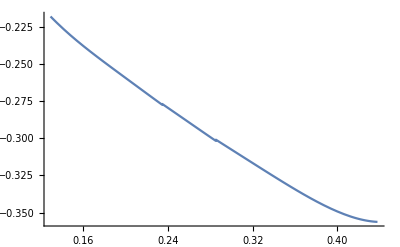

```mathematica
Plot[x interpF2[[1]]'[x]/interpF2[[1]][x],{x,interpF2[[1]][[1,1,1]],interpF2[[1]][[1,1,2]]},PlotRange->All]
```

```mathematica
Plot[interpF2[[1]][x],{x,interpF2[[1]][[1,1,1]],interpF2[[1]][[1,1,2]]},PlotRange->All]
```

```mathematica
LogLinearPlot[-x^2(-interp'[x]^2+interp[x] interp''[x])/interp[x]^2,{x,interp[[1,1,1]],interp[[1,1,2]]},GridLines->{{},{{2,Red},{3,Red}}},PlotRange->{All,All}]
```

```mathematica
Data={{params[[2;;5]],Sort[Partition[Riffle[T[tempstamp],Stable],2],#2[[2]]<#1[[2]]&]}}
```

```mathematica
Data=Join[{{params[[2;;7]],Sort[Partition[Riffle[T[tempstamp],Stable],2],#2[[2]]<#1[[2]]&]}},Data];
```

```mathematica
DeleteDuplicates[Data[[All,1]]]
```

```mathematica
Data>>TData;
```

```mathematica
Data=<<TData;
```

```mathematica
Data[[All,1]]
```

```mathematica
Tstep3=Reverse[Tstep3];
tempstamp=Reverse[tempstamp];
```

```mathematica
BinaryWrite["data",Flatten[Tstep3[[-1]]],type];
Close["data"];
```

```mathematica
Data[[All,1]]
```

```mathematica
PlotData=Sort[Select[Data,#[[1,{5,6}]]=={params[[6]],params[[7]]}&],#1[[1,2]]<#2[[1,2]]&];
```

```mathematica
PlotData[[All,1]]
```

```mathematica
PlotData=PlotData[[{1,3,4,7}]];
```

```mathematica
inter=Map[Interpolation[#[[2]],InterpolationOrder->5]&,PlotData]
```

```mathematica
LogLinearPlot[Evaluate[Flatten[Table[x inter[[i]]'[x]/inter[[i]][x],{i,1,Length[inter]}]]],{x,inter[[1,1,1,1]],inter[[1,1,1,2]]},PlotLegends->Placed[Table["A="<>ToString[PlotData[[i,1,2]]]<>",k/μ="<>ToString[(2 π)/PlotData[[i,1,1]]],{i,1,Length[inter]}],{0.85,0.7}],Frame->True,FrameStyle->17,GridLines->{{},{{3,{Dashed,Red,Thick}},{2,{Dashed,Red,Thick}}}},FrameLabel->{"T/μ","T dS/dT"}]
```

```mathematica
legend=Join[Table["A="<>ToString[PlotData[[i,1,2]]],{i,1,1}],Table["A="<>ToString[PlotData[[i,1,2]]]<>",k/μ="<>ToString[(2 π)/PlotData[[i,1,1]]],{i,2,Length[inter]}]]
```

```mathematica
LogLinearPlot[Evaluate[Flatten[Table[x inter[[i]]'[x]/inter[[i]][x],{i,1,Length[inter]}]]],{x,inter[[1,1,1,1]],inter[[1,1,1,2]]},PlotLegends->Placed[legend,{0.85,0.7}],Frame->True,FrameStyle->17,GridLines->{{},{{3,{Dashed,Red,Thick}},{2,{Dashed,Red,Thick}}}},FrameLabel->{"T/μ","T dS/dT"}]
```

## Lattice Leading Operator

```mathematica
ldata=Partition[Riffle[T[tempstamp],Re[Fourier[#,FourierParameters->{-1,-1}][[1]]&/@√(1+Tstep3[[All,3,-1]])]],2];
```

```mathematica
linter=Interpolation[DeleteDuplicates[ldata]]
```

InterpolatingFunction[{{0.0000797175,0.000207108}},<>]

```mathematica
LogLinearPlot[linter[x],{x,linter[[1,1,1]],linter[[1,1,2]]}]
```

```mathematica
linter[0]
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

1.03444

```mathematica
LogLinearPlot[x linter'[x]/linter[x],{x,linter[[1,1,1]],linter[[1,1,2]]}]
```

```mathematica
LogLinearPlot[1+x linter''[x]/linter'[x],{x,linter[[1,1,1]],linter[[1,1,2]]}]
```

```mathematica
ν=1/2 √(5+4 ((2 π)/(params[[2]] linter[0]))^2-4 √(1+2 ((2 π)/(params[[2]] linter[0]))^2))-1/2
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

0.105096

```mathematica
power=2 ν
```

0.210192

## ξ^2-Einstein’s-Scalar test

Commands

```mathematica
ccheck=Compile[{{Q11Val,_Real,2},{Q22Val,_Real,2},{QrrVal,_Real,2},{QttVal,_Real,2},{Qr1Val,_Real,2},{Qt2Val,_Real,2},μ,L,{grid,_Real,1}},(((2 L^2 grid⟦2;;-1+NpTT⟧^2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)^2 Q11Val⟦2;;-1+NpTT⟧^2 Q22Val⟦2;;-1+NpTT⟧^2 Qr1Val⟦2;;-1+NpTT⟧^2 QrrVal⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧^2+Q11Val⟦2;;-1+NpTT⟧^2 Q22Val⟦2;;-1+NpTT⟧^2 QrrVal⟦2;;-1+NpTT⟧ (-QrrVal⟦2;;-1+NpTT⟧^2 (1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧))+2 (-1+grid⟦2;;-1+NpTT⟧)^2 Qt2Val⟦2;;-1+NpTT⟧^2)+1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧)) QttVal⟦2;;-1+NpTT⟧^2)+2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (Q22Val⟦2;;-1+NpTT⟧^2 QrrVal⟦2;;-1+NpTT⟧^3 QttVal⟦2;;-1+NpTT⟧^2+grid⟦2;;-1+NpTT⟧ Q11Val⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧^2 QrrVal⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧^2 (-grid⟦2;;-1+NpTT⟧ Qr1Val⟦2;;-1+NpTT⟧ d[0,1][Q11Val]⟦2;;-1+NpTT⟧+d[1,0][Q11Val]⟦2;;-1+NpTT⟧)+Q11Val⟦2;;-1+NpTT⟧^2 (QrrVal⟦2;;-1+NpTT⟧^3 QttVal⟦2;;-1+NpTT⟧^2+grid⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧^2 (-grid⟦2;;-1+NpTT⟧ Qr1Val⟦2;;-1+NpTT⟧ d[0,1][Q22Val]⟦2;;-1+NpTT⟧+d[1,0][Q22Val]⟦2;;-1+NpTT⟧)+Q22Val⟦2;;-1+NpTT⟧^2 (QrrVal⟦2;;-1+NpTT⟧^3+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧^2 (grid⟦2;;-1+NpTT⟧ Qr1Val⟦2;;-1+NpTT⟧ d[0,1][QrrVal]⟦2;;-1+NpTT⟧-d[1,0][QrrVal]⟦2;;-1+NpTT⟧)-QrrVal⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧ (QttVal⟦2;;-1+NpTT⟧ (3+grid⟦2;;-1+NpTT⟧^2 d[0,1][Qr1Val]⟦2;;-1+NpTT⟧)+grid⟦2;;-1+NpTT⟧ (grid⟦2;;-1+NpTT⟧ Qr1Val⟦2;;-1+NpTT⟧ d[0,1][QttVal]⟦2;;-1+NpTT⟧-d[1,0][QttVal]⟦2;;-1+NpTT⟧)))))) (2 L^4 grid⟦2;;-1+NpTT⟧^4 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)^3 Q11Val⟦2;;-1+NpTT⟧^4 Q22Val⟦2;;-1+NpTT⟧^2 Qr1Val⟦2;;-1+NpTT⟧^4 QttVal⟦2;;-1+NpTT⟧^2+Q11Val⟦2;;-1+NpTT⟧^2 Q22Val⟦2;;-1+NpTT⟧^2 QrrVal⟦2;;-1+NpTT⟧^2 (-QrrVal⟦2;;-1+NpTT⟧^2 (1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧))+2 (-1+grid⟦2;;-1+NpTT⟧)^2 Qt2Val⟦2;;-1+NpTT⟧^2)+1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧)) QttVal⟦2;;-1+NpTT⟧^2)+2 L^2 grid⟦2;;-1+NpTT⟧^2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)^2 Q11Val⟦2;;-1+NpTT⟧^2 Qr1Val⟦2;;-1+NpTT⟧ (2 Q22Val⟦2;;-1+NpTT⟧^2 Qr1Val⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧^2 QttVal⟦2;;-1+NpTT⟧^2+Q11Val⟦2;;-1+NpTT⟧^2 (Qr1Val⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧^2 QttVal⟦2;;-1+NpTT⟧^2+Q22Val⟦2;;-1+NpTT⟧^2 (Qr1Val⟦2;;-1+NpTT⟧ (QrrVal⟦2;;-1+NpTT⟧^2+grid⟦2;;-1+NpTT⟧^2 QttVal⟦2;;-1+NpTT⟧^2 d[0,1][Qr1Val]⟦2;;-1+NpTT⟧)-grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧^2 d[1,0][Qr1Val]⟦2;;-1+NpTT⟧)))-(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (-2 Q22Val⟦2;;-1+NpTT⟧^2 QrrVal⟦2;;-1+NpTT⟧^4 QttVal⟦2;;-1+NpTT⟧^2+L^2 grid⟦2;;-1+NpTT⟧^2 Q11Val⟦2;;-1+NpTT⟧^4 Q22Val⟦2;;-1+NpTT⟧^2 Qr1Val⟦2;;-1+NpTT⟧^2 (QrrVal⟦2;;-1+NpTT⟧^2 (1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧))+2 (-1+grid⟦2;;-1+NpTT⟧)^2 Qt2Val⟦2;;-1+NpTT⟧^2)+1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧)) QttVal⟦2;;-1+NpTT⟧^2)+2 grid⟦2;;-1+NpTT⟧ Q11Val⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧^2 QrrVal⟦2;;-1+NpTT⟧^2 QttVal⟦2;;-1+NpTT⟧^2 (2 grid⟦2;;-1+NpTT⟧ Qr1Val⟦2;;-1+NpTT⟧ d[0,1][Q11Val]⟦2;;-1+NpTT⟧-d[1,0][Q11Val]⟦2;;-1+NpTT⟧)-2 Q11Val⟦2;;-1+NpTT⟧^2 QrrVal⟦2;;-1+NpTT⟧ (QrrVal⟦2;;-1+NpTT⟧^3 QttVal⟦2;;-1+NpTT⟧^2+grid⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧^2 d[1,0][Q22Val]⟦2;;-1+NpTT⟧+Q22Val⟦2;;-1+NpTT⟧^2 (QrrVal⟦2;;-1+NpTT⟧^3+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧^2 (2 grid⟦2;;-1+NpTT⟧ Qr1Val⟦2;;-1+NpTT⟧ d[0,1][QrrVal]⟦2;;-1+NpTT⟧-d[1,0][QrrVal]⟦2;;-1+NpTT⟧)+QrrVal⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧ (-QttVal⟦2;;-1+NpTT⟧ (3+grid⟦2;;-1+NpTT⟧^2 d[0,1][Qr1Val]⟦2;;-1+NpTT⟧)+grid⟦2;;-1+NpTT⟧ d[1,0][QttVal]⟦2;;-1+NpTT⟧))))))/(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)+1/L^2 2 grid⟦2;;-1+NpTT⟧^2 Q22Val⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧ (2 L^4 grid⟦2;;-1+NpTT⟧^2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)^2 Q11Val⟦2;;-1+NpTT⟧^3 Q22Val⟦2;;-1+NpTT⟧^2 Qr1Val⟦2;;-1+NpTT⟧^3 QttVal⟦2;;-1+NpTT⟧^2-Q22Val⟦2;;-1+NpTT⟧ (L^2 Q11Val⟦2;;-1+NpTT⟧^3 Q22Val⟦2;;-1+NpTT⟧ Qr1Val⟦2;;-1+NpTT⟧ (QrrVal⟦2;;-1+NpTT⟧^2 (1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧))+2 (-1+grid⟦2;;-1+NpTT⟧)^2 Qt2Val⟦2;;-1+NpTT⟧^2)+1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧)) QttVal⟦2;;-1+NpTT⟧^2)+2 Q22Val⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧^2 QttVal⟦2;;-1+NpTT⟧^2 d[0,1][Q11Val]⟦2;;-1+NpTT⟧-2 Q11Val⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧ (Q22Val⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧ d[0,1][QrrVal]⟦2;;-1+NpTT⟧+QrrVal⟦2;;-1+NpTT⟧ (QttVal⟦2;;-1+NpTT⟧ d[0,1][Q22Val]⟦2;;-1+NpTT⟧+Q22Val⟦2;;-1+NpTT⟧ d[0,1][QttVal]⟦2;;-1+NpTT⟧)))+2 L^2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) Q11Val⟦2;;-1+NpTT⟧ (Q22Val⟦2;;-1+NpTT⟧^2 Qr1Val⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧^2 QttVal⟦2;;-1+NpTT⟧^2+Q11Val⟦2;;-1+NpTT⟧^2 (Qr1Val⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧^2 QttVal⟦2;;-1+NpTT⟧^2+Q22Val⟦2;;-1+NpTT⟧^2 (Qr1Val⟦2;;-1+NpTT⟧ (QrrVal⟦2;;-1+NpTT⟧^2+grid⟦2;;-1+NpTT⟧^2 QttVal⟦2;;-1+NpTT⟧^2 d[0,1][Qr1Val]⟦2;;-1+NpTT⟧)-grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧^2 d[1,0][Qr1Val]⟦2;;-1+NpTT⟧)))) (QrrVal⟦2;;-1+NpTT⟧ (-1/2 L^2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧)) Q11Val⟦2;;-1+NpTT⟧^3 Q22Val⟦2;;-1+NpTT⟧ Qr1Val⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧-Q22Val⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧^2 QttVal⟦2;;-1+NpTT⟧ d[0,1][Q11Val]⟦2;;-1+NpTT⟧+Q11Val⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧ (Q22Val⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧ d[0,1][QrrVal]⟦2;;-1+NpTT⟧+QrrVal⟦2;;-1+NpTT⟧ (QttVal⟦2;;-1+NpTT⟧ d[0,1][Q22Val]⟦2;;-1+NpTT⟧+Q22Val⟦2;;-1+NpTT⟧ d[0,1][QttVal]⟦2;;-1+NpTT⟧)))+L^2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) Q11Val⟦2;;-1+NpTT⟧^2 (grid⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧ Qr1Val⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧ (grid⟦2;;-1+NpTT⟧ Qr1Val⟦2;;-1+NpTT⟧ d[0,1][Q11Val]⟦2;;-1+NpTT⟧-d[1,0][Q11Val]⟦2;;-1+NpTT⟧)+Q11Val⟦2;;-1+NpTT⟧ (grid⟦2;;-1+NpTT⟧ Qr1Val⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧ (grid⟦2;;-1+NpTT⟧ Qr1Val⟦2;;-1+NpTT⟧ d[0,1][Q22Val]⟦2;;-1+NpTT⟧-d[1,0][Q22Val]⟦2;;-1+NpTT⟧)+Q22Val⟦2;;-1+NpTT⟧ (grid⟦2;;-1+NpTT⟧^2 Qr1Val⟦2;;-1+NpTT⟧^2 (-QttVal⟦2;;-1+NpTT⟧ d[0,1][QrrVal]⟦2;;-1+NpTT⟧+QrrVal⟦2;;-1+NpTT⟧ d[0,1][QttVal]⟦2;;-1+NpTT⟧)-grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧ d[1,0][Qr1Val]⟦2;;-1+NpTT⟧+Qr1Val⟦2;;-1+NpTT⟧ (grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧ d[1,0][QrrVal]⟦2;;-1+NpTT⟧+QrrVal⟦2;;-1+NpTT⟧ (QttVal⟦2;;-1+NpTT⟧ (3+2 grid⟦2;;-1+NpTT⟧^2 d[0,1][Qr1Val]⟦2;;-1+NpTT⟧)-grid⟦2;;-1+NpTT⟧ d[1,0][QttVal]⟦2;;-1+NpTT⟧)))))))/(4 Q11Val⟦2;;-1+NpTT⟧^4 Q22Val⟦2;;-1+NpTT⟧^4 QrrVal⟦2;;-1+NpTT⟧^5 QttVal⟦2;;-1+NpTT⟧^4),Parallelization->True,RuntimeAttributes->Listable];
```

```mathematica
check[var_,μ_,L_,grid_]:=ccheck[√(1+grid var[[3]]),√(1+grid var[[5]]),√(1+grid var[[2]]),√(1+grid var[[1]]), 1/L var[[4]],0 var[[4]],μ,L,grid]
```

```mathematica
ccheckEOM=Compile[{{Q11Val,_Real,2},{Q22Val,_Real,2},{QrrVal,_Real,2},{QttVal,_Real,2},{Qr1Val,_Real,2},{hVal,_Real,2},μ,L,A1,{grid,_Real,1}},(ⅇ^(-(2 μ grid⟦2;;-1+NpTT⟧ hVal⟦2;;-1+NpTT⟧)/(3 A1)) grid⟦2;;-1+NpTT⟧^16 (1/grid⟦2;;-1+NpTT⟧^6(2+3 A1^2) ⅇ^((2 μ grid⟦2;;-1+NpTT⟧ hVal⟦2;;-1+NpTT⟧)/(3 A1)) (1+grid⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧) (1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) (1/grid⟦2;;-1+NpTT⟧^6(1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) d[0,1][Q11Val]⟦2;;-1+NpTT⟧ d[0,1][Q22Val]⟦2;;-1+NpTT⟧+1/grid⟦2;;-1+NpTT⟧^2(1+grid⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧) (1/grid⟦2;;-1+NpTT⟧^2(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) Qr1Val⟦2;;-1+NpTT⟧^2 (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) (d[0,1][Q11Val]⟦2;;-1+NpTT⟧)^2+1/grid⟦2;;-1+NpTT⟧^4(1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧) d[0,1][Q11Val]⟦2;;-1+NpTT⟧ d[0,1][QttVal]⟦2;;-1+NpTT⟧-1/grid⟦2;;-1+NpTT⟧^5 2 L (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) Qr1Val⟦2;;-1+NpTT⟧ (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) d[0,1][Q11Val]⟦2;;-1+NpTT⟧ (-2-grid⟦2;;-1+NpTT⟧ Q11Val⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][Q11Val]⟦2;;-1+NpTT⟧)+1/grid⟦2;;-1+NpTT⟧^2(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) ((d[0,1][Q11Val]⟦2;;-1+NpTT⟧ d[0,1][QrrVal]⟦2;;-1+NpTT⟧)/(grid⟦2;;-1+NpTT⟧^2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3))+1/grid⟦2;;-1+NpTT⟧^6 L^2 (-2-grid⟦2;;-1+NpTT⟧ Q11Val⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][Q11Val]⟦2;;-1+NpTT⟧)^2)))-1/grid⟦2;;-1+NpTT⟧^2(2+3 A1^2) ⅇ^((2 μ grid⟦2;;-1+NpTT⟧ hVal⟦2;;-1+NpTT⟧)/(3 A1)) (1+grid⟦2;;-1+NpTT⟧ Q11Val⟦2;;-1+NpTT⟧) (-1/grid⟦2;;-1+NpTT⟧^10(1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧)^2 (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧)^2 (d[0,1][Q22Val]⟦2;;-1+NpTT⟧)^2+1/grid⟦2;;-1+NpTT⟧^6(1+grid⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧) (1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) (1/grid⟦2;;-1+NpTT⟧^2(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) Qr1Val⟦2;;-1+NpTT⟧^2 (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) d[0,1][Q11Val]⟦2;;-1+NpTT⟧ d[0,1][Q22Val]⟦2;;-1+NpTT⟧+1/grid⟦2;;-1+NpTT⟧^4(1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧) d[0,1][Q22Val]⟦2;;-1+NpTT⟧ d[0,1][QttVal]⟦2;;-1+NpTT⟧-1/grid⟦2;;-1+NpTT⟧L (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) Qr1Val⟦2;;-1+NpTT⟧ (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) (1/grid⟦2;;-1+NpTT⟧^4 d[0,1][Q22Val]⟦2;;-1+NpTT⟧ (-2-grid⟦2;;-1+NpTT⟧ Q11Val⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][Q11Val]⟦2;;-1+NpTT⟧)+1/grid⟦2;;-1+NpTT⟧^4 d[0,1][Q11Val]⟦2;;-1+NpTT⟧ (-2-grid⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][Q22Val]⟦2;;-1+NpTT⟧))+1/grid⟦2;;-1+NpTT⟧^2(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) ((d[0,1][Q22Val]⟦2;;-1+NpTT⟧ d[0,1][QrrVal]⟦2;;-1+NpTT⟧)/(grid⟦2;;-1+NpTT⟧^2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3))+(2 (1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧) d[0,2][Q22Val]⟦2;;-1+NpTT⟧)/(grid⟦2;;-1+NpTT⟧^3 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3))+1/grid⟦2;;-1+NpTT⟧^6 L^2 (-2-grid⟦2;;-1+NpTT⟧ Q11Val⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][Q11Val]⟦2;;-1+NpTT⟧) (-2-grid⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][Q22Val]⟦2;;-1+NpTT⟧)))+1/grid⟦2;;-1+NpTT⟧^4(1+grid⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧)^2 (((1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧)^2 (1/grid⟦2;;-1+NpTT⟧^2 2 μ^2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)^2 (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧)^2 (d[0,1][hVal]⟦2;;-1+NpTT⟧)^2-((2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)^2 (d[0,1][QttVal]⟦2;;-1+NpTT⟧)^2)/grid⟦2;;-1+NpTT⟧^2+1/grid⟦2;;-1+NpTT⟧^3 2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)^2 (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) d[0,2][QttVal]⟦2;;-1+NpTT⟧))/(grid⟦2;;-1+NpTT⟧^4 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)^2)-1/grid⟦2;;-1+NpTT⟧^4(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)^2 (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧)^2 ((Qr1Val⟦2;;-1+NpTT⟧^2 d[0,1][Q11Val]⟦2;;-1+NpTT⟧ d[0,1][QrrVal]⟦2;;-1+NpTT⟧)/(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)+(d[0,1][QrrVal]⟦2;;-1+NpTT⟧)^2/(grid⟦2;;-1+NpTT⟧^2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)^2)+(L^2 (-2-grid⟦2;;-1+NpTT⟧ Q11Val⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][Q11Val]⟦2;;-1+NpTT⟧) (-1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧)) (1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧)+(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (-2-grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][QrrVal]⟦2;;-1+NpTT⟧)))/(grid⟦2;;-1+NpTT⟧^6 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)^2)-L grid⟦2;;-1+NpTT⟧ Qr1Val⟦2;;-1+NpTT⟧ ((d[0,1][QrrVal]⟦2;;-1+NpTT⟧ (-2-grid⟦2;;-1+NpTT⟧ Q11Val⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][Q11Val]⟦2;;-1+NpTT⟧))/(grid⟦2;;-1+NpTT⟧^4 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3))+(d[0,1][Q11Val]⟦2;;-1+NpTT⟧ (-1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧)) (1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧)+(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (-2-grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][QrrVal]⟦2;;-1+NpTT⟧)))/(grid⟦2;;-1+NpTT⟧^4 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)^2)))+1/grid⟦2;;-1+NpTT⟧^4(1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) ((d[0,1][QrrVal]⟦2;;-1+NpTT⟧ d[0,1][QttVal]⟦2;;-1+NpTT⟧)/grid⟦2;;-1+NpTT⟧^2+grid⟦2;;-1+NpTT⟧^2 Qr1Val⟦2;;-1+NpTT⟧^2 (1/grid⟦2;;-1+NpTT⟧^2(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) d[0,1][Q11Val]⟦2;;-1+NpTT⟧ d[0,1][QttVal]⟦2;;-1+NpTT⟧+1/grid⟦2;;-1+NpTT⟧^3 2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) d[0,2][Q11Val]⟦2;;-1+NpTT⟧)+(2 (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) d[0,2][QrrVal]⟦2;;-1+NpTT⟧)/grid⟦2;;-1+NpTT⟧^3-1/grid⟦2;;-1+NpTT⟧^4 4 L (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) d[0,1][Qr1Val]⟦2;;-1+NpTT⟧ (-2-grid⟦2;;-1+NpTT⟧ Q11Val⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][Q11Val]⟦2;;-1+NpTT⟧)-1/grid⟦2;;-1+NpTT⟧^3 2 L (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) d[0,1][Q11Val]⟦2;;-1+NpTT⟧ (Qr1Val⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧ d[1,0][Qr1Val]⟦2;;-1+NpTT⟧)+1/grid⟦2;;-1+NpTT⟧^6 L^2 (-2-grid⟦2;;-1+NpTT⟧ Q11Val⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][Q11Val]⟦2;;-1+NpTT⟧) (1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧)) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧)+(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (-2-grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][QttVal]⟦2;;-1+NpTT⟧))-grid⟦2;;-1+NpTT⟧ Qr1Val⟦2;;-1+NpTT⟧ (L (1/grid⟦2;;-1+NpTT⟧^4(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) d[0,1][QttVal]⟦2;;-1+NpTT⟧ (-2-grid⟦2;;-1+NpTT⟧ Q11Val⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][Q11Val]⟦2;;-1+NpTT⟧)+1/grid⟦2;;-1+NpTT⟧^4 d[0,1][Q11Val]⟦2;;-1+NpTT⟧ (1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧)) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧)+(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (-2-grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][QttVal]⟦2;;-1+NpTT⟧)))+1/grid⟦2;;-1+NpTT⟧^2(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) (-6 d[0,1][Q11Val]⟦2;;-1+NpTT⟧ d[0,1][Qr1Val]⟦2;;-1+NpTT⟧+(4 L (-d[0,1][Q11Val]⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧ d[1,1][Q11Val]⟦2;;-1+NpTT⟧))/grid⟦2;;-1+NpTT⟧^2))+1/grid⟦2;;-1+NpTT⟧^6 2 L^2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) (6+2 grid⟦2;;-1+NpTT⟧ Q11Val⟦2;;-1+NpTT⟧-2 grid⟦2;;-1+NpTT⟧^2 d[1,0][Q11Val]⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^3 d[2,0][Q11Val]⟦2;;-1+NpTT⟧))))+1/grid⟦2;;-1+NpTT⟧^4(1+grid⟦2;;-1+NpTT⟧ Q11Val⟦2;;-1+NpTT⟧)^2 (1/grid⟦2;;-1+NpTT⟧^6(2+3 A1^2) ⅇ^((2 μ grid⟦2;;-1+NpTT⟧ hVal⟦2;;-1+NpTT⟧)/(3 A1)) (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧)^2 (Qr1Val⟦2;;-1+NpTT⟧ d[0,1][Q22Val]⟦2;;-1+NpTT⟧-1/grid⟦2;;-1+NpTT⟧^3 L (-2-grid⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][Q22Val]⟦2;;-1+NpTT⟧))^2-1/grid⟦2;;-1+NpTT⟧^4(2+3 A1^2) ⅇ^((2 μ grid⟦2;;-1+NpTT⟧ hVal⟦2;;-1+NpTT⟧)/(3 A1)) (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (1+grid⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) (grid⟦2;;-1+NpTT⟧^2 Qr1Val⟦2;;-1+NpTT⟧^2 (1/grid⟦2;;-1+NpTT⟧^4(1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧) d[0,1][Q22Val]⟦2;;-1+NpTT⟧ d[0,1][QttVal]⟦2;;-1+NpTT⟧+1/grid⟦2;;-1+NpTT⟧^2(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) (-(d[0,1][Q22Val]⟦2;;-1+NpTT⟧ d[0,1][QrrVal]⟦2;;-1+NpTT⟧)/(grid⟦2;;-1+NpTT⟧^2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3))+(2 (1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧) d[0,2][Q22Val]⟦2;;-1+NpTT⟧)/(grid⟦2;;-1+NpTT⟧^3 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3))))+grid⟦2;;-1+NpTT⟧ Qr1Val⟦2;;-1+NpTT⟧ (1/grid⟦2;;-1+NpTT⟧^2 L (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) ((d[0,1][QrrVal]⟦2;;-1+NpTT⟧ (-2-grid⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][Q22Val]⟦2;;-1+NpTT⟧))/(grid⟦2;;-1+NpTT⟧^4 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3))+(d[0,1][Q22Val]⟦2;;-1+NpTT⟧ (-1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧)) (1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧)+(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (-2-grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][QrrVal]⟦2;;-1+NpTT⟧)))/(grid⟦2;;-1+NpTT⟧^4 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)^2))-((1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧) (L (1/grid⟦2;;-1+NpTT⟧^4(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) d[0,1][QttVal]⟦2;;-1+NpTT⟧ (-2-grid⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][Q22Val]⟦2;;-1+NpTT⟧)+1/grid⟦2;;-1+NpTT⟧^4 d[0,1][Q22Val]⟦2;;-1+NpTT⟧ (1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧)) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧)+(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (-2-grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][QttVal]⟦2;;-1+NpTT⟧)))+1/grid⟦2;;-1+NpTT⟧^2(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) (-4 d[0,1][Q22Val]⟦2;;-1+NpTT⟧ d[0,1][Qr1Val]⟦2;;-1+NpTT⟧+(4 L (-d[0,1][Q22Val]⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧ d[1,1][Q22Val]⟦2;;-1+NpTT⟧))/grid⟦2;;-1+NpTT⟧^2)))/(grid⟦2;;-1+NpTT⟧^2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)))+L (-(L (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) (-2-grid⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][Q22Val]⟦2;;-1+NpTT⟧) (-1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧)) (1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧)+(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (-2-grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][QrrVal]⟦2;;-1+NpTT⟧)))/(grid⟦2;;-1+NpTT⟧^8 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3))+((1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧) (1/grid⟦2;;-1+NpTT⟧^6 L (-2-grid⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][Q22Val]⟦2;;-1+NpTT⟧) (1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧)) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧)+(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (-2-grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][QttVal]⟦2;;-1+NpTT⟧))-1/grid⟦2;;-1+NpTT⟧^2 2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) (1/grid⟦2;;-1+NpTT⟧^2 d[0,1][Qr1Val]⟦2;;-1+NpTT⟧ (-2-grid⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][Q22Val]⟦2;;-1+NpTT⟧)+1/grid⟦2;;-1+NpTT⟧d[0,1][Q22Val]⟦2;;-1+NpTT⟧ (Qr1Val⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧ d[1,0][Qr1Val]⟦2;;-1+NpTT⟧)-1/grid⟦2;;-1+NpTT⟧^4 L (6+2 grid⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧-2 grid⟦2;;-1+NpTT⟧^2 d[1,0][Q22Val]⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^3 d[2,0][Q22Val]⟦2;;-1+NpTT⟧))))/(grid⟦2;;-1+NpTT⟧^2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3))))+1/grid⟦2;;-1+NpTT⟧^4(1+grid⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧)^2 (1/grid⟦2;;-1+NpTT⟧^8 48 (3 A1^2+2 ⅇ^((2/(3 A1)+A1) μ grid⟦2;;-1+NpTT⟧ hVal⟦2;;-1+NpTT⟧)) L^2 (1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧)^2 (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧)^2+1/grid⟦2;;-1+NpTT⟧^2(2+3 A1^2) ⅇ^((2 μ grid⟦2;;-1+NpTT⟧ hVal⟦2;;-1+NpTT⟧)/(3 A1)) (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) ((Qr1Val⟦2;;-1+NpTT⟧ d[0,1][QrrVal]⟦2;;-1+NpTT⟧)/(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)-(L (-1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧)) (1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧)+(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (-2-grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][QrrVal]⟦2;;-1+NpTT⟧)))/(grid⟦2;;-1+NpTT⟧^3 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)^2)) (1/grid⟦2;;-1+NpTT⟧2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) d[0,1][Qr1Val]⟦2;;-1+NpTT⟧+(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) Qr1Val⟦2;;-1+NpTT⟧ d[0,1][QttVal]⟦2;;-1+NpTT⟧-1/grid⟦2;;-1+NpTT⟧^3 L (1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧)) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧)+(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (-2-grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][QttVal]⟦2;;-1+NpTT⟧)))-((2+3 A1^2) ⅇ^((2 μ grid⟦2;;-1+NpTT⟧ hVal⟦2;;-1+NpTT⟧)/(3 A1)) (1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧) (grid⟦2;;-1+NpTT⟧^2 Qr1Val⟦2;;-1+NpTT⟧^2 (1/grid⟦2;;-1+NpTT⟧^2 2 μ^2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)^2 (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧)^2 (d[0,1][hVal]⟦2;;-1+NpTT⟧)^2-1/grid⟦2;;-1+NpTT⟧^2(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)^2 (d[0,1][QttVal]⟦2;;-1+NpTT⟧)^2+1/grid⟦2;;-1+NpTT⟧^3 2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)^2 (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) d[0,2][QttVal]⟦2;;-1+NpTT⟧)-1/grid⟦2;;-1+NpTT⟧^6 L^2 (1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧)) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧)+(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (-2-grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][QttVal]⟦2;;-1+NpTT⟧))^2+1/grid⟦2;;-1+NpTT⟧^4 2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)^2 (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧)^2 (2 grid⟦2;;-1+NpTT⟧^2 (d[0,1][Qr1Val]⟦2;;-1+NpTT⟧)^2+L^2 μ^2 (hVal⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧ d[1,0][hVal]⟦2;;-1+NpTT⟧)^2-2 L (d[0,1][Qr1Val]⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧ d[1,1][Qr1Val]⟦2;;-1+NpTT⟧))+2 grid⟦2;;-1+NpTT⟧ Qr1Val⟦2;;-1+NpTT⟧ (1/grid⟦2;;-1+NpTT⟧^4 2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)^2 (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧)^2 (grid⟦2;;-1+NpTT⟧ d[0,2][Qr1Val]⟦2;;-1+NpTT⟧-L μ^2 grid⟦2;;-1+NpTT⟧ d[0,1][hVal]⟦2;;-1+NpTT⟧ (hVal⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧ d[1,0][hVal]⟦2;;-1+NpTT⟧))+1/grid⟦2;;-1+NpTT⟧^4 L (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) d[0,1][QttVal]⟦2;;-1+NpTT⟧ (1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧)) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧)+(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (-2-grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][QttVal]⟦2;;-1+NpTT⟧))+1/grid⟦2;;-1+NpTT⟧^2 2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) ((2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) d[0,1][Qr1Val]⟦2;;-1+NpTT⟧ d[0,1][QttVal]⟦2;;-1+NpTT⟧-1/grid⟦2;;-1+NpTT⟧^2 L ((-2-1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3+1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧))) d[0,1][QttVal]⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧ (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) d[1,1][QttVal]⟦2;;-1+NpTT⟧)))+1/grid⟦2;;-1+NpTT⟧^2 2 L (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) (-1/grid⟦2;;-1+NpTT⟧(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) d[0,1][QttVal]⟦2;;-1+NpTT⟧ (Qr1Val⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧ d[1,0][Qr1Val]⟦2;;-1+NpTT⟧)-1/grid⟦2;;-1+NpTT⟧^2 d[0,1][Qr1Val]⟦2;;-1+NpTT⟧ (1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧)) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧)+(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (-2-grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][QttVal]⟦2;;-1+NpTT⟧))+1/grid⟦2;;-1+NpTT⟧^4 L (grid⟦2;;-1+NpTT⟧ (3 grid⟦2;;-1+NpTT⟧^2 (-4+μ^2 (-1+2 grid⟦2;;-1+NpTT⟧)) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧)+grid⟦2;;-1+NpTT⟧^2 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧)) (-2-grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][QttVal]⟦2;;-1+NpTT⟧))+(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (6+2 grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧-2 grid⟦2;;-1+NpTT⟧^2 d[1,0][QttVal]⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^3 d[2,0][QttVal]⟦2;;-1+NpTT⟧)))))/(grid⟦2;;-1+NpTT⟧^2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3))))))/(2 (2+3 A1^2) L^2 (1+grid⟦2;;-1+NpTT⟧ Q11Val⟦2;;-1+NpTT⟧)^2 (1+grid⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧)^2 (1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧)^2 (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧)^2),Parallelization->True,RuntimeAttributes->Listable];
```

```mathematica
ccheckSC=Compile[{{Q11Val,_Real,2},{Q22Val,_Real,2},{QrrVal,_Real,2},{QttVal,_Real,2},{Qr1Val,_Real,2},{hVal,_Real,2},{a0Val,_Real,2},μ,L,A1,B1,{grid,_Real,1}},1/2 (-(24 A1 (ⅇ^(-(2 μ grid⟦2;;-1+NpTT⟧ hVal⟦2;;-1+NpTT⟧)/(3 A1))-ⅇ^(A1 μ grid⟦2;;-1+NpTT⟧ hVal⟦2;;-1+NpTT⟧)))/(2+3 A1^2)+(grid⟦2;;-1+NpTT⟧^12 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (-(μ (1+grid⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧) (1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧)^2 (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) d[0,1][hVal]⟦2;;-1+NpTT⟧ d[0,1][Q11Val]⟦2;;-1+NpTT⟧)/(grid⟦2;;-1+NpTT⟧^8 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3))+((1+grid⟦2;;-1+NpTT⟧ Q11Val⟦2;;-1+NpTT⟧) (1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧) (1/grid⟦2;;-1+NpTT⟧^4 μ (1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) d[0,1][hVal]⟦2;;-1+NpTT⟧ d[0,1][Q22Val]⟦2;;-1+NpTT⟧+1/grid⟦2;;-1+NpTT⟧^2(1+grid⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧) (1/grid⟦2;;-1+NpTT⟧μ (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) d[0,1][hVal]⟦2;;-1+NpTT⟧ (grid⟦2;;-1+NpTT⟧ Qr1Val⟦2;;-1+NpTT⟧^2 d[0,1][Q11Val]⟦2;;-1+NpTT⟧+(d[0,1][QrrVal]⟦2;;-1+NpTT⟧)/(grid⟦2;;-1+NpTT⟧ (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)))+((1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧) (B1 ⅇ^(B1 μ grid⟦2;;-1+NpTT⟧ hVal⟦2;;-1+NpTT⟧) μ^2 (-1+grid⟦2;;-1+NpTT⟧)^2 (d[0,1][a0Val]⟦2;;-1+NpTT⟧)^2+μ (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) d[0,1][hVal]⟦2;;-1+NpTT⟧ d[0,1][QttVal]⟦2;;-1+NpTT⟧+1/grid⟦2;;-1+NpTT⟧2 μ (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) d[0,2][hVal]⟦2;;-1+NpTT⟧))/(grid⟦2;;-1+NpTT⟧^2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3))+1/grid⟦2;;-1+NpTT⟧^2 L (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) (-μ Qr1Val⟦2;;-1+NpTT⟧ d[0,1][Q11Val]⟦2;;-1+NpTT⟧ (hVal⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧ d[1,0][hVal]⟦2;;-1+NpTT⟧)+1/grid⟦2;;-1+NpTT⟧^3(-μ grid⟦2;;-1+NpTT⟧^2 Qr1Val⟦2;;-1+NpTT⟧ d[0,1][hVal]⟦2;;-1+NpTT⟧+L μ (hVal⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧ d[1,0][hVal]⟦2;;-1+NpTT⟧)) (-2-grid⟦2;;-1+NpTT⟧ Q11Val⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][Q11Val]⟦2;;-1+NpTT⟧)))))/(grid⟦2;;-1+NpTT⟧^4 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3))+1/grid⟦2;;-1+NpTT⟧^4(1+grid⟦2;;-1+NpTT⟧ Q11Val⟦2;;-1+NpTT⟧)^2 (1/grid⟦2;;-1+NpTT⟧^4(1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) (μ grid⟦2;;-1+NpTT⟧^2 Qr1Val⟦2;;-1+NpTT⟧ d[0,1][hVal]⟦2;;-1+NpTT⟧-L μ (hVal⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧ d[1,0][hVal]⟦2;;-1+NpTT⟧)) (Qr1Val⟦2;;-1+NpTT⟧ d[0,1][Q22Val]⟦2;;-1+NpTT⟧-1/grid⟦2;;-1+NpTT⟧^3 L (-2-grid⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][Q22Val]⟦2;;-1+NpTT⟧))+1/grid⟦2;;-1+NpTT⟧^2(1+grid⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧) (grid⟦2;;-1+NpTT⟧^2 Qr1Val⟦2;;-1+NpTT⟧^2 (-1/grid⟦2;;-1+NpTT⟧^2 μ (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) d[0,1][hVal]⟦2;;-1+NpTT⟧ d[0,1][QrrVal]⟦2;;-1+NpTT⟧+((1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧) (B1 ⅇ^(B1 μ grid⟦2;;-1+NpTT⟧ hVal⟦2;;-1+NpTT⟧) μ^2 (-1+grid⟦2;;-1+NpTT⟧)^2 (d[0,1][a0Val]⟦2;;-1+NpTT⟧)^2+μ (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) d[0,1][hVal]⟦2;;-1+NpTT⟧ d[0,1][QttVal]⟦2;;-1+NpTT⟧+1/grid⟦2;;-1+NpTT⟧2 μ (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) d[0,2][hVal]⟦2;;-1+NpTT⟧))/(grid⟦2;;-1+NpTT⟧^2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)))+grid⟦2;;-1+NpTT⟧ Qr1Val⟦2;;-1+NpTT⟧ (1/grid⟦2;;-1+NpTT⟧^2 L (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) ((μ d[0,1][QrrVal]⟦2;;-1+NpTT⟧ (hVal⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧ d[1,0][hVal]⟦2;;-1+NpTT⟧))/(grid⟦2;;-1+NpTT⟧ (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3))+(μ d[0,1][hVal]⟦2;;-1+NpTT⟧ (-1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧)) (1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧)+(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (-2-grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][QrrVal]⟦2;;-1+NpTT⟧)))/(grid⟦2;;-1+NpTT⟧^2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)^2))-((1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧) (L (-2 B1 ⅇ^(B1 μ grid⟦2;;-1+NpTT⟧ hVal⟦2;;-1+NpTT⟧) μ (-1+grid⟦2;;-1+NpTT⟧) d[0,1][a0Val]⟦2;;-1+NpTT⟧ (-μ a0Val⟦2;;-1+NpTT⟧-μ (-1+grid⟦2;;-1+NpTT⟧) d[1,0][a0Val]⟦2;;-1+NpTT⟧)+1/grid⟦2;;-1+NpTT⟧μ (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) d[0,1][QttVal]⟦2;;-1+NpTT⟧ (hVal⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧ d[1,0][hVal]⟦2;;-1+NpTT⟧))+μ grid⟦2;;-1+NpTT⟧ d[0,1][hVal]⟦2;;-1+NpTT⟧ (-1/grid⟦2;;-1+NpTT⟧4 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) d[0,1][Qr1Val]⟦2;;-1+NpTT⟧+1/grid⟦2;;-1+NpTT⟧^3 L (1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧)) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧)+(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (-2-grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][QttVal]⟦2;;-1+NpTT⟧)))+1/grid⟦2;;-1+NpTT⟧^2 4 L μ (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) (d[0,1][hVal]⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧ d[1,1][hVal]⟦2;;-1+NpTT⟧)))/(grid⟦2;;-1+NpTT⟧^2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)))+L (-(L μ (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) (hVal⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧ d[1,0][hVal]⟦2;;-1+NpTT⟧) (-1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧)) (1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧)+(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (-2-grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][QrrVal]⟦2;;-1+NpTT⟧)))/(grid⟦2;;-1+NpTT⟧^5 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3))+((1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧) (B1 ⅇ^(B1 μ grid⟦2;;-1+NpTT⟧ hVal⟦2;;-1+NpTT⟧) L (-μ a0Val⟦2;;-1+NpTT⟧-μ (-1+grid⟦2;;-1+NpTT⟧) d[1,0][a0Val]⟦2;;-1+NpTT⟧)^2+1/grid⟦2;;-1+NpTT⟧^3 L μ (hVal⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧ d[1,0][hVal]⟦2;;-1+NpTT⟧) (1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧)) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧)+(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (-2-grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][QttVal]⟦2;;-1+NpTT⟧))-1/grid⟦2;;-1+NpTT⟧^2 2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) (μ grid⟦2;;-1+NpTT⟧ d[0,1][Qr1Val]⟦2;;-1+NpTT⟧ (hVal⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧ d[1,0][hVal]⟦2;;-1+NpTT⟧)+μ grid⟦2;;-1+NpTT⟧ d[0,1][hVal]⟦2;;-1+NpTT⟧ (Qr1Val⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧ d[1,0][Qr1Val]⟦2;;-1+NpTT⟧)-L μ (2 d[1,0][hVal]⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧ d[2,0][hVal]⟦2;;-1+NpTT⟧))))/(grid⟦2;;-1+NpTT⟧^2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)))))))/(L^2 (1+grid⟦2;;-1+NpTT⟧ Q11Val⟦2;;-1+NpTT⟧)^2 (1+grid⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧) (1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧)^2 (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧))),Parallelization->True,RuntimeAttributes->Listable];
```

```mathematica
checkEOM[var_,μ_,L_,A1_,grid_]:=ccheckEOM[var[[3]],var[[5]],var[[2]],var[[1]], var[[4]],var[[7]],μ,L,A1,grid]
```

```mathematica
checkSC[var_,μ_,L_,A1_,B1_,grid_]:=ccheckSC[var[[3]],var[[5]],var[[2]],var[[1]], var[[4]],var[[7]],var[[6]],μ,L,A1,B1,grid]
```

Commands HP

```mathematica
ccheck[Q11Val_,Q22Val_,QrrVal_,QttVal_,Qr1Val_,Qt2Val_,μ_,L_,grid_]:=(((2 L^2 grid⟦2;;-1+NpTT⟧^2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)^2 Q11Val⟦2;;-1+NpTT⟧^2 Q22Val⟦2;;-1+NpTT⟧^2 Qr1Val⟦2;;-1+NpTT⟧^2 QrrVal⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧^2+Q11Val⟦2;;-1+NpTT⟧^2 Q22Val⟦2;;-1+NpTT⟧^2 QrrVal⟦2;;-1+NpTT⟧ (-QrrVal⟦2;;-1+NpTT⟧^2 (1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧))+2 (-1+grid⟦2;;-1+NpTT⟧)^2 Qt2Val⟦2;;-1+NpTT⟧^2)+1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧)) QttVal⟦2;;-1+NpTT⟧^2)+2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (Q22Val⟦2;;-1+NpTT⟧^2 QrrVal⟦2;;-1+NpTT⟧^3 QttVal⟦2;;-1+NpTT⟧^2+grid⟦2;;-1+NpTT⟧ Q11Val⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧^2 QrrVal⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧^2 (-grid⟦2;;-1+NpTT⟧ Qr1Val⟦2;;-1+NpTT⟧ d[0,1][Q11Val]⟦2;;-1+NpTT⟧+d[1,0][Q11Val]⟦2;;-1+NpTT⟧)+Q11Val⟦2;;-1+NpTT⟧^2 (QrrVal⟦2;;-1+NpTT⟧^3 QttVal⟦2;;-1+NpTT⟧^2+grid⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧^2 (-grid⟦2;;-1+NpTT⟧ Qr1Val⟦2;;-1+NpTT⟧ d[0,1][Q22Val]⟦2;;-1+NpTT⟧+d[1,0][Q22Val]⟦2;;-1+NpTT⟧)+Q22Val⟦2;;-1+NpTT⟧^2 (QrrVal⟦2;;-1+NpTT⟧^3+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧^2 (grid⟦2;;-1+NpTT⟧ Qr1Val⟦2;;-1+NpTT⟧ d[0,1][QrrVal]⟦2;;-1+NpTT⟧-d[1,0][QrrVal]⟦2;;-1+NpTT⟧)-QrrVal⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧ (QttVal⟦2;;-1+NpTT⟧ (3+grid⟦2;;-1+NpTT⟧^2 d[0,1][Qr1Val]⟦2;;-1+NpTT⟧)+grid⟦2;;-1+NpTT⟧ (grid⟦2;;-1+NpTT⟧ Qr1Val⟦2;;-1+NpTT⟧ d[0,1][QttVal]⟦2;;-1+NpTT⟧-d[1,0][QttVal]⟦2;;-1+NpTT⟧)))))) (2 L^4 grid⟦2;;-1+NpTT⟧^4 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)^3 Q11Val⟦2;;-1+NpTT⟧^4 Q22Val⟦2;;-1+NpTT⟧^2 Qr1Val⟦2;;-1+NpTT⟧^4 QttVal⟦2;;-1+NpTT⟧^2+Q11Val⟦2;;-1+NpTT⟧^2 Q22Val⟦2;;-1+NpTT⟧^2 QrrVal⟦2;;-1+NpTT⟧^2 (-QrrVal⟦2;;-1+NpTT⟧^2 (1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧))+2 (-1+grid⟦2;;-1+NpTT⟧)^2 Qt2Val⟦2;;-1+NpTT⟧^2)+1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧)) QttVal⟦2;;-1+NpTT⟧^2)+2 L^2 grid⟦2;;-1+NpTT⟧^2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)^2 Q11Val⟦2;;-1+NpTT⟧^2 Qr1Val⟦2;;-1+NpTT⟧ (2 Q22Val⟦2;;-1+NpTT⟧^2 Qr1Val⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧^2 QttVal⟦2;;-1+NpTT⟧^2+Q11Val⟦2;;-1+NpTT⟧^2 (Qr1Val⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧^2 QttVal⟦2;;-1+NpTT⟧^2+Q22Val⟦2;;-1+NpTT⟧^2 (Qr1Val⟦2;;-1+NpTT⟧ (QrrVal⟦2;;-1+NpTT⟧^2+grid⟦2;;-1+NpTT⟧^2 QttVal⟦2;;-1+NpTT⟧^2 d[0,1][Qr1Val]⟦2;;-1+NpTT⟧)-grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧^2 d[1,0][Qr1Val]⟦2;;-1+NpTT⟧)))-(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (-2 Q22Val⟦2;;-1+NpTT⟧^2 QrrVal⟦2;;-1+NpTT⟧^4 QttVal⟦2;;-1+NpTT⟧^2+L^2 grid⟦2;;-1+NpTT⟧^2 Q11Val⟦2;;-1+NpTT⟧^4 Q22Val⟦2;;-1+NpTT⟧^2 Qr1Val⟦2;;-1+NpTT⟧^2 (QrrVal⟦2;;-1+NpTT⟧^2 (1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧))+2 (-1+grid⟦2;;-1+NpTT⟧)^2 Qt2Val⟦2;;-1+NpTT⟧^2)+1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧)) QttVal⟦2;;-1+NpTT⟧^2)+2 grid⟦2;;-1+NpTT⟧ Q11Val⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧^2 QrrVal⟦2;;-1+NpTT⟧^2 QttVal⟦2;;-1+NpTT⟧^2 (2 grid⟦2;;-1+NpTT⟧ Qr1Val⟦2;;-1+NpTT⟧ d[0,1][Q11Val]⟦2;;-1+NpTT⟧-d[1,0][Q11Val]⟦2;;-1+NpTT⟧)-2 Q11Val⟦2;;-1+NpTT⟧^2 QrrVal⟦2;;-1+NpTT⟧ (QrrVal⟦2;;-1+NpTT⟧^3 QttVal⟦2;;-1+NpTT⟧^2+grid⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧^2 d[1,0][Q22Val]⟦2;;-1+NpTT⟧+Q22Val⟦2;;-1+NpTT⟧^2 (QrrVal⟦2;;-1+NpTT⟧^3+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧^2 (2 grid⟦2;;-1+NpTT⟧ Qr1Val⟦2;;-1+NpTT⟧ d[0,1][QrrVal]⟦2;;-1+NpTT⟧-d[1,0][QrrVal]⟦2;;-1+NpTT⟧)+QrrVal⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧ (-QttVal⟦2;;-1+NpTT⟧ (3+grid⟦2;;-1+NpTT⟧^2 d[0,1][Qr1Val]⟦2;;-1+NpTT⟧)+grid⟦2;;-1+NpTT⟧ d[1,0][QttVal]⟦2;;-1+NpTT⟧))))))/(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)+1/L^2 2 grid⟦2;;-1+NpTT⟧^2 Q22Val⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧ (2 L^4 grid⟦2;;-1+NpTT⟧^2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)^2 Q11Val⟦2;;-1+NpTT⟧^3 Q22Val⟦2;;-1+NpTT⟧^2 Qr1Val⟦2;;-1+NpTT⟧^3 QttVal⟦2;;-1+NpTT⟧^2-Q22Val⟦2;;-1+NpTT⟧ (L^2 Q11Val⟦2;;-1+NpTT⟧^3 Q22Val⟦2;;-1+NpTT⟧ Qr1Val⟦2;;-1+NpTT⟧ (QrrVal⟦2;;-1+NpTT⟧^2 (1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧))+2 (-1+grid⟦2;;-1+NpTT⟧)^2 Qt2Val⟦2;;-1+NpTT⟧^2)+1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧)) QttVal⟦2;;-1+NpTT⟧^2)+2 Q22Val⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧^2 QttVal⟦2;;-1+NpTT⟧^2 d[0,1][Q11Val]⟦2;;-1+NpTT⟧-2 Q11Val⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧ (Q22Val⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧ d[0,1][QrrVal]⟦2;;-1+NpTT⟧+QrrVal⟦2;;-1+NpTT⟧ (QttVal⟦2;;-1+NpTT⟧ d[0,1][Q22Val]⟦2;;-1+NpTT⟧+Q22Val⟦2;;-1+NpTT⟧ d[0,1][QttVal]⟦2;;-1+NpTT⟧)))+2 L^2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) Q11Val⟦2;;-1+NpTT⟧ (Q22Val⟦2;;-1+NpTT⟧^2 Qr1Val⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧^2 QttVal⟦2;;-1+NpTT⟧^2+Q11Val⟦2;;-1+NpTT⟧^2 (Qr1Val⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧^2 QttVal⟦2;;-1+NpTT⟧^2+Q22Val⟦2;;-1+NpTT⟧^2 (Qr1Val⟦2;;-1+NpTT⟧ (QrrVal⟦2;;-1+NpTT⟧^2+grid⟦2;;-1+NpTT⟧^2 QttVal⟦2;;-1+NpTT⟧^2 d[0,1][Qr1Val]⟦2;;-1+NpTT⟧)-grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧^2 d[1,0][Qr1Val]⟦2;;-1+NpTT⟧)))) (QrrVal⟦2;;-1+NpTT⟧ (-1/2 L^2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧)) Q11Val⟦2;;-1+NpTT⟧^3 Q22Val⟦2;;-1+NpTT⟧ Qr1Val⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧-Q22Val⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧^2 QttVal⟦2;;-1+NpTT⟧ d[0,1][Q11Val]⟦2;;-1+NpTT⟧+Q11Val⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧ (Q22Val⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧ d[0,1][QrrVal]⟦2;;-1+NpTT⟧+QrrVal⟦2;;-1+NpTT⟧ (QttVal⟦2;;-1+NpTT⟧ d[0,1][Q22Val]⟦2;;-1+NpTT⟧+Q22Val⟦2;;-1+NpTT⟧ d[0,1][QttVal]⟦2;;-1+NpTT⟧)))+L^2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) Q11Val⟦2;;-1+NpTT⟧^2 (grid⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧ Qr1Val⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧ (grid⟦2;;-1+NpTT⟧ Qr1Val⟦2;;-1+NpTT⟧ d[0,1][Q11Val]⟦2;;-1+NpTT⟧-d[1,0][Q11Val]⟦2;;-1+NpTT⟧)+Q11Val⟦2;;-1+NpTT⟧ (grid⟦2;;-1+NpTT⟧ Qr1Val⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧ (grid⟦2;;-1+NpTT⟧ Qr1Val⟦2;;-1+NpTT⟧ d[0,1][Q22Val]⟦2;;-1+NpTT⟧-d[1,0][Q22Val]⟦2;;-1+NpTT⟧)+Q22Val⟦2;;-1+NpTT⟧ (grid⟦2;;-1+NpTT⟧^2 Qr1Val⟦2;;-1+NpTT⟧^2 (-QttVal⟦2;;-1+NpTT⟧ d[0,1][QrrVal]⟦2;;-1+NpTT⟧+QrrVal⟦2;;-1+NpTT⟧ d[0,1][QttVal]⟦2;;-1+NpTT⟧)-grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧ d[1,0][Qr1Val]⟦2;;-1+NpTT⟧+Qr1Val⟦2;;-1+NpTT⟧ (grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧ d[1,0][QrrVal]⟦2;;-1+NpTT⟧+QrrVal⟦2;;-1+NpTT⟧ (QttVal⟦2;;-1+NpTT⟧ (3+2 grid⟦2;;-1+NpTT⟧^2 d[0,1][Qr1Val]⟦2;;-1+NpTT⟧)-grid⟦2;;-1+NpTT⟧ d[1,0][QttVal]⟦2;;-1+NpTT⟧)))))))/(4 Q11Val⟦2;;-1+NpTT⟧^4 Q22Val⟦2;;-1+NpTT⟧^4 QrrVal⟦2;;-1+NpTT⟧^5 QttVal⟦2;;-1+NpTT⟧^4)
```

```mathematica
ccheckConstraints[Q11Val_,Q22Val_,QrrVal_,QttVal_,Qr1Val_,hVal_,a0Val_,AxVal_,h11Val_,httVal_,h22Val_,ht1Val_,A0Val_,DhVal_,μ_,L_,A1_,B1_,ω_,muj_,grid_]:=-(48 A1 ⅇ^(-(2 μ grid⟦2;;-2⟧ hVal⟦2;;-2⟧)/(3 A1)) DhVal⟦2;;-2⟧ grid⟦2;;-2⟧)/(2+3 A1^2)+(48 A1 ⅇ^(A1 μ grid⟦2;;-2⟧ hVal⟦2;;-2⟧) DhVal⟦2;;-2⟧ grid⟦2;;-2⟧)/(2+3 A1^2)+(18 ⅈ ω (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^6 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) h22Val⟦2;;-2⟧)/((-12+μ^2) (-1+grid⟦2;;-2⟧^3)^2 (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+(36 ω^2 (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^6 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) h22Val⟦2;;-2⟧)/((-12+μ^2)^2 (-1+grid⟦2;;-2⟧^3)^2 (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-(18 ⅈ ω (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^7 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) h22Val⟦2;;-2⟧)/((-12+μ^2) (-1+grid⟦2;;-2⟧^3)^2 (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-(36 ω^2 (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^7 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) h22Val⟦2;;-2⟧)/((-12+μ^2)^2 (-1+grid⟦2;;-2⟧^3)^2 (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-(12 ⅈ ω (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^3 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) h22Val⟦2;;-2⟧)/((-12+μ^2) (-1+grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+(24 ⅈ ω (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^4 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) h22Val⟦2;;-2⟧)/((-12+μ^2) (-1+grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-(9 ⅈ ω (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^6 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) httVal⟦2;;-2⟧)/((-12+μ^2) (-1+grid⟦2;;-2⟧^3)^2 (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-(18 ω^2 (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^6 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) httVal⟦2;;-2⟧)/((-12+μ^2)^2 (-1+grid⟦2;;-2⟧^3)^2 (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+(6 ⅈ ω (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^3 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) httVal⟦2;;-2⟧)/((-12+μ^2) (-1+grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-(4 ω^2 grid⟦2;;-2⟧^2 h22Val⟦2;;-2⟧)/((-1+grid⟦2;;-2⟧) (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧))+(4 ω^2 grid⟦2;;-2⟧^3 h22Val⟦2;;-2⟧)/((-1+grid⟦2;;-2⟧) (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧))-(2 (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^3 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧ d[0,1][h22Val]⟦2;;-2⟧)/(L (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+(12 ⅈ ω (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^5 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧ d[0,1][h22Val]⟦2;;-2⟧)/(L (-12+μ^2) (-1+grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-(12 ⅈ ω (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^6 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧ d[0,1][h22Val]⟦2;;-2⟧)/(L (-12+μ^2) (-1+grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+(2 ⅈ ω grid⟦2;;-2⟧^2 d[0,1][ht1Val]⟦2;;-2⟧)/(L (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧))-(6 ⅈ ω (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^5 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧ d[0,1][httVal]⟦2;;-2⟧)/(L (-12+μ^2) (-1+grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+(μ DhVal⟦2;;-2⟧ (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^4 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧ d[0,1][hVal]⟦2;;-2⟧)/(L (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+(6 ⅈ μ ω DhVal⟦2;;-2⟧ (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^7 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧ d[0,1][hVal]⟦2;;-2⟧)/(L (-12+μ^2) (-1+grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-(2 μ grid⟦2;;-2⟧^4 d[0,1][DhVal]⟦2;;-2⟧ d[0,1][hVal]⟦2;;-2⟧)/(L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧))-1/(L^2 (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))μ (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^6 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧^2 d[0,1][DhVal]⟦2;;-2⟧ d[0,1][hVal]⟦2;;-2⟧+(μ^2 grid⟦2;;-2⟧^4 h11Val⟦2;;-2⟧ (d[0,1][hVal]⟦2;;-2⟧)^2)/(L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧))+(μ^2 grid⟦2;;-2⟧^4 h22Val⟦2;;-2⟧ (d[0,1][hVal]⟦2;;-2⟧)^2)/(L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧))-(μ^2 grid⟦2;;-2⟧^5 h22Val⟦2;;-2⟧ (d[0,1][hVal]⟦2;;-2⟧)^2)/(L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧))-(ⅈ ω grid⟦2;;-2⟧^3 ht1Val⟦2;;-2⟧ d[0,1][Q11Val]⟦2;;-2⟧)/(L (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧)^2)+(3 ⅈ ω (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^6 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) h11Val⟦2;;-2⟧ Qr1Val⟦2;;-2⟧ d[0,1][Q11Val]⟦2;;-2⟧)/(2 L (-12+μ^2) (-1+grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-(3 (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^4 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) h22Val⟦2;;-2⟧ Qr1Val⟦2;;-2⟧ d[0,1][Q11Val]⟦2;;-2⟧)/(4 L (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+(9 ⅈ ω (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^6 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) h22Val⟦2;;-2⟧ Qr1Val⟦2;;-2⟧ d[0,1][Q11Val]⟦2;;-2⟧)/(2 L (-12+μ^2) (-1+grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-(9 ⅈ ω (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^7 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) h22Val⟦2;;-2⟧ Qr1Val⟦2;;-2⟧ d[0,1][Q11Val]⟦2;;-2⟧)/(2 L (-12+μ^2) (-1+grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-(3 ⅈ ω (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^6 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) httVal⟦2;;-2⟧ Qr1Val⟦2;;-2⟧ d[0,1][Q11Val]⟦2;;-2⟧)/(2 L (-12+μ^2) (-1+grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-(grid⟦2;;-2⟧^3 d[0,1][h11Val]⟦2;;-2⟧ d[0,1][Q11Val]⟦2;;-2⟧)/(2 L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧)^2)-((-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^5 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧^2 d[0,1][h11Val]⟦2;;-2⟧ d[0,1][Q11Val]⟦2;;-2⟧)/(4 L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+(grid⟦2;;-2⟧^3 d[0,1][h22Val]⟦2;;-2⟧ d[0,1][Q11Val]⟦2;;-2⟧)/(2 L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧)^2)-(grid⟦2;;-2⟧^4 d[0,1][h22Val]⟦2;;-2⟧ d[0,1][Q11Val]⟦2;;-2⟧)/(2 L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧)^2)-(3 (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^5 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧^2 d[0,1][h22Val]⟦2;;-2⟧ d[0,1][Q11Val]⟦2;;-2⟧)/(4 L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+(3 (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^6 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧^2 d[0,1][h22Val]⟦2;;-2⟧ d[0,1][Q11Val]⟦2;;-2⟧)/(4 L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-(grid⟦2;;-2⟧^3 d[0,1][httVal]⟦2;;-2⟧ d[0,1][Q11Val]⟦2;;-2⟧)/(2 L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧)^2)+((-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^5 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧^2 d[0,1][httVal]⟦2;;-2⟧ d[0,1][Q11Val]⟦2;;-2⟧)/(4 L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+(ⅈ ω grid⟦2;;-2⟧^3 ht1Val⟦2;;-2⟧ d[0,1][Q22Val]⟦2;;-2⟧)/(L (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧))-(3 ⅈ ω (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^6 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) h11Val⟦2;;-2⟧ Qr1Val⟦2;;-2⟧ d[0,1][Q22Val]⟦2;;-2⟧)/(2 L (-12+μ^2) (-1+grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-(3 (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^4 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) h22Val⟦2;;-2⟧ Qr1Val⟦2;;-2⟧ d[0,1][Q22Val]⟦2;;-2⟧)/(4 L (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+(9 ⅈ ω (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^6 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) h22Val⟦2;;-2⟧ Qr1Val⟦2;;-2⟧ d[0,1][Q22Val]⟦2;;-2⟧)/(2 L (-12+μ^2) (-1+grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-(9 ⅈ ω (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^7 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) h22Val⟦2;;-2⟧ Qr1Val⟦2;;-2⟧ d[0,1][Q22Val]⟦2;;-2⟧)/(2 L (-12+μ^2) (-1+grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-(3 ⅈ ω (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^6 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) httVal⟦2;;-2⟧ Qr1Val⟦2;;-2⟧ d[0,1][Q22Val]⟦2;;-2⟧)/(2 L (-12+μ^2) (-1+grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+(3 grid⟦2;;-2⟧^3 d[0,1][h11Val]⟦2;;-2⟧ d[0,1][Q22Val]⟦2;;-2⟧)/(2 L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧))+((-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^5 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧^2 d[0,1][h11Val]⟦2;;-2⟧ d[0,1][Q22Val]⟦2;;-2⟧)/(4 L^2 (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-(grid⟦2;;-2⟧^3 d[0,1][h22Val]⟦2;;-2⟧ d[0,1][Q22Val]⟦2;;-2⟧)/(2 L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧))+(grid⟦2;;-2⟧^4 d[0,1][h22Val]⟦2;;-2⟧ d[0,1][Q22Val]⟦2;;-2⟧)/(2 L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧))-(3 (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^5 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧^2 d[0,1][h22Val]⟦2;;-2⟧ d[0,1][Q22Val]⟦2;;-2⟧)/(4 L^2 (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+(3 (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^6 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧^2 d[0,1][h22Val]⟦2;;-2⟧ d[0,1][Q22Val]⟦2;;-2⟧)/(4 L^2 (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+(grid⟦2;;-2⟧^3 d[0,1][httVal]⟦2;;-2⟧ d[0,1][Q22Val]⟦2;;-2⟧)/(2 L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧))+((-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^5 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧^2 d[0,1][httVal]⟦2;;-2⟧ d[0,1][Q22Val]⟦2;;-2⟧)/(4 L^2 (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-(grid⟦2;;-2⟧^4 h11Val⟦2;;-2⟧ d[0,1][Q11Val]⟦2;;-2⟧ d[0,1][Q22Val]⟦2;;-2⟧)/(2 L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧)^2 (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧))-(grid⟦2;;-2⟧^4 h22Val⟦2;;-2⟧ d[0,1][Q11Val]⟦2;;-2⟧ d[0,1][Q22Val]⟦2;;-2⟧)/(2 L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧)^2 (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧))+(grid⟦2;;-2⟧^5 h22Val⟦2;;-2⟧ d[0,1][Q11Val]⟦2;;-2⟧ d[0,1][Q22Val]⟦2;;-2⟧)/(2 L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧)^2 (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧))-(grid⟦2;;-2⟧^4 h11Val⟦2;;-2⟧ (d[0,1][Q22Val]⟦2;;-2⟧)^2)/(2 L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧)^2)-(grid⟦2;;-2⟧^4 h22Val⟦2;;-2⟧ (d[0,1][Q22Val]⟦2;;-2⟧)^2)/(2 L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧)^2)+(grid⟦2;;-2⟧^5 h22Val⟦2;;-2⟧ (d[0,1][Q22Val]⟦2;;-2⟧)^2)/(2 L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧)^2)+(3 ⅈ ω (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^5 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) h11Val⟦2;;-2⟧ d[0,1][Qr1Val]⟦2;;-2⟧)/(L (-12+μ^2) (-1+grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-(3 (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^3 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) h22Val⟦2;;-2⟧ d[0,1][Qr1Val]⟦2;;-2⟧)/(2 L (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+(9 ⅈ ω (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^5 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) h22Val⟦2;;-2⟧ d[0,1][Qr1Val]⟦2;;-2⟧)/(L (-12+μ^2) (-1+grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-(9 ⅈ ω (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^6 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) h22Val⟦2;;-2⟧ d[0,1][Qr1Val]⟦2;;-2⟧)/(L (-12+μ^2) (-1+grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-(3 ⅈ ω (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^5 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) httVal⟦2;;-2⟧ d[0,1][Qr1Val]⟦2;;-2⟧)/(L (-12+μ^2) (-1+grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-((-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^4 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧ d[0,1][h11Val]⟦2;;-2⟧ d[0,1][Qr1Val]⟦2;;-2⟧)/(2 L^2 (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-(5 (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^4 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧ d[0,1][h22Val]⟦2;;-2⟧ d[0,1][Qr1Val]⟦2;;-2⟧)/(2 L^2 (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+(5 (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^5 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧ d[0,1][h22Val]⟦2;;-2⟧ d[0,1][Qr1Val]⟦2;;-2⟧)/(2 L^2 (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+1/(L^2 (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))(-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^4 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧ d[0,1][httVal]⟦2;;-2⟧ d[0,1][Qr1Val]⟦2;;-2⟧+((-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^4 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) h22Val⟦2;;-2⟧ Qr1Val⟦2;;-2⟧ d[0,1][QrrVal]⟦2;;-2⟧)/(2 L (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧)^2)-(3 ⅈ ω (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^6 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) h22Val⟦2;;-2⟧ Qr1Val⟦2;;-2⟧ d[0,1][QrrVal]⟦2;;-2⟧)/(L (-12+μ^2) (-1+grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧)^2)+(3 ⅈ ω (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^7 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) h22Val⟦2;;-2⟧ Qr1Val⟦2;;-2⟧ d[0,1][QrrVal]⟦2;;-2⟧)/(L (-12+μ^2) (-1+grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧)^2)+(3 ⅈ ω (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^6 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) httVal⟦2;;-2⟧ Qr1Val⟦2;;-2⟧ d[0,1][QrrVal]⟦2;;-2⟧)/(2 L (-12+μ^2) (-1+grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧)^2)+(ⅈ ω grid⟦2;;-2⟧^3 ht1Val⟦2;;-2⟧ d[0,1][QrrVal]⟦2;;-2⟧)/(L (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+(grid⟦2;;-2⟧^3 d[0,1][h11Val]⟦2;;-2⟧ d[0,1][QrrVal]⟦2;;-2⟧)/(L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+((-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^5 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧^2 d[0,1][h22Val]⟦2;;-2⟧ d[0,1][QrrVal]⟦2;;-2⟧)/(2 L^2 (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧)^2)-((-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^6 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧^2 d[0,1][h22Val]⟦2;;-2⟧ d[0,1][QrrVal]⟦2;;-2⟧)/(2 L^2 (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧)^2)-((-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^5 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧^2 d[0,1][httVal]⟦2;;-2⟧ d[0,1][QrrVal]⟦2;;-2⟧)/(4 L^2 (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧)^2)+(grid⟦2;;-2⟧^3 d[0,1][httVal]⟦2;;-2⟧ d[0,1][QrrVal]⟦2;;-2⟧)/(2 L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-(grid⟦2;;-2⟧^4 h11Val⟦2;;-2⟧ d[0,1][Q11Val]⟦2;;-2⟧ d[0,1][QrrVal]⟦2;;-2⟧)/(2 L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧)^2 (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-(grid⟦2;;-2⟧^4 h22Val⟦2;;-2⟧ d[0,1][Q11Val]⟦2;;-2⟧ d[0,1][QrrVal]⟦2;;-2⟧)/(2 L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧)^2 (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+(grid⟦2;;-2⟧^5 h22Val⟦2;;-2⟧ d[0,1][Q11Val]⟦2;;-2⟧ d[0,1][QrrVal]⟦2;;-2⟧)/(2 L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧)^2 (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+(grid⟦2;;-2⟧^4 h11Val⟦2;;-2⟧ d[0,1][Q22Val]⟦2;;-2⟧ d[0,1][QrrVal]⟦2;;-2⟧)/(2 L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+(grid⟦2;;-2⟧^4 h22Val⟦2;;-2⟧ d[0,1][Q22Val]⟦2;;-2⟧ d[0,1][QrrVal]⟦2;;-2⟧)/(2 L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-(grid⟦2;;-2⟧^5 h22Val⟦2;;-2⟧ d[0,1][Q22Val]⟦2;;-2⟧ d[0,1][QrrVal]⟦2;;-2⟧)/(2 L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-(grid⟦2;;-2⟧^4 h11Val⟦2;;-2⟧ (d[0,1][QrrVal]⟦2;;-2⟧)^2)/(2 L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧)^2)-(grid⟦2;;-2⟧^4 h22Val⟦2;;-2⟧ (d[0,1][QrrVal]⟦2;;-2⟧)^2)/(2 L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧)^2)+(grid⟦2;;-2⟧^5 h22Val⟦2;;-2⟧ (d[0,1][QrrVal]⟦2;;-2⟧)^2)/(2 L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧)^2)+(2 ⅈ ω grid⟦2;;-2⟧^3 ht1Val⟦2;;-2⟧ d[0,1][QttVal]⟦2;;-2⟧)/(L (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧))-((-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^4 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) h22Val⟦2;;-2⟧ Qr1Val⟦2;;-2⟧ d[0,1][QttVal]⟦2;;-2⟧)/(2 L (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧))+(3 ⅈ ω (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^6 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) h22Val⟦2;;-2⟧ Qr1Val⟦2;;-2⟧ d[0,1][QttVal]⟦2;;-2⟧)/(L (-12+μ^2) (-1+grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧))-(3 ⅈ ω (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^7 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) h22Val⟦2;;-2⟧ Qr1Val⟦2;;-2⟧ d[0,1][QttVal]⟦2;;-2⟧)/(L (-12+μ^2) (-1+grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧))-(3 ⅈ ω (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^6 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) httVal⟦2;;-2⟧ Qr1Val⟦2;;-2⟧ d[0,1][QttVal]⟦2;;-2⟧)/(L (-12+μ^2) (-1+grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧))+(grid⟦2;;-2⟧^3 d[0,1][h11Val]⟦2;;-2⟧ d[0,1][QttVal]⟦2;;-2⟧)/(L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧))-((-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^5 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧^2 d[0,1][h22Val]⟦2;;-2⟧ d[0,1][QttVal]⟦2;;-2⟧)/(2 L^2 (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧))+((-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^6 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧^2 d[0,1][h22Val]⟦2;;-2⟧ d[0,1][QttVal]⟦2;;-2⟧)/(2 L^2 (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧))+(grid⟦2;;-2⟧^3 d[0,1][httVal]⟦2;;-2⟧ d[0,1][QttVal]⟦2;;-2⟧)/(L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧))+((-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^5 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧^2 d[0,1][httVal]⟦2;;-2⟧ d[0,1][QttVal]⟦2;;-2⟧)/(2 L^2 (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧))-(grid⟦2;;-2⟧^4 h11Val⟦2;;-2⟧ d[0,1][Q11Val]⟦2;;-2⟧ d[0,1][QttVal]⟦2;;-2⟧)/(2 L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧)^2 (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧))-(grid⟦2;;-2⟧^4 h22Val⟦2;;-2⟧ d[0,1][Q11Val]⟦2;;-2⟧ d[0,1][QttVal]⟦2;;-2⟧)/(2 L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧)^2 (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧))+(grid⟦2;;-2⟧^5 h22Val⟦2;;-2⟧ d[0,1][Q11Val]⟦2;;-2⟧ d[0,1][QttVal]⟦2;;-2⟧)/(2 L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧)^2 (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧))+(grid⟦2;;-2⟧^4 h11Val⟦2;;-2⟧ d[0,1][Q22Val]⟦2;;-2⟧ d[0,1][QttVal]⟦2;;-2⟧)/(2 L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧))+(grid⟦2;;-2⟧^4 h22Val⟦2;;-2⟧ d[0,1][Q22Val]⟦2;;-2⟧ d[0,1][QttVal]⟦2;;-2⟧)/(2 L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧))-(grid⟦2;;-2⟧^5 h22Val⟦2;;-2⟧ d[0,1][Q22Val]⟦2;;-2⟧ d[0,1][QttVal]⟦2;;-2⟧)/(2 L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧))+(grid⟦2;;-2⟧^4 h11Val⟦2;;-2⟧ d[0,1][QrrVal]⟦2;;-2⟧ d[0,1][QttVal]⟦2;;-2⟧)/(2 L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧))+(grid⟦2;;-2⟧^4 h22Val⟦2;;-2⟧ d[0,1][QrrVal]⟦2;;-2⟧ d[0,1][QttVal]⟦2;;-2⟧)/(2 L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧))-(grid⟦2;;-2⟧^5 h22Val⟦2;;-2⟧ d[0,1][QrrVal]⟦2;;-2⟧ d[0,1][QttVal]⟦2;;-2⟧)/(2 L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧))-(grid⟦2;;-2⟧^4 h11Val⟦2;;-2⟧ (d[0,1][QttVal]⟦2;;-2⟧)^2)/(2 L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧)^2)-(grid⟦2;;-2⟧^4 h22Val⟦2;;-2⟧ (d[0,1][QttVal]⟦2;;-2⟧)^2)/(2 L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧)^2)+(grid⟦2;;-2⟧^5 h22Val⟦2;;-2⟧ (d[0,1][QttVal]⟦2;;-2⟧)^2)/(2 L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧)^2)+(grid⟦2;;-2⟧^2 d[0,2][h11Val]⟦2;;-2⟧)/(L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧))-(grid⟦2;;-2⟧^2 d[0,2][h22Val]⟦2;;-2⟧)/(L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧))+(grid⟦2;;-2⟧^3 d[0,2][h22Val]⟦2;;-2⟧)/(L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧))-((-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^4 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧^2 d[0,2][h22Val]⟦2;;-2⟧)/(L^2 (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+((-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^5 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧^2 d[0,2][h22Val]⟦2;;-2⟧)/(L^2 (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+(grid⟦2;;-2⟧^2 d[0,2][httVal]⟦2;;-2⟧)/(L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧))+((-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^4 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧^2 d[0,2][httVal]⟦2;;-2⟧)/(2 L^2 (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+(grid⟦2;;-2⟧^3 h11Val⟦2;;-2⟧ d[0,2][Q22Val]⟦2;;-2⟧)/(L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧))+(grid⟦2;;-2⟧^3 h22Val⟦2;;-2⟧ d[0,2][Q22Val]⟦2;;-2⟧)/(L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧))-(grid⟦2;;-2⟧^4 h22Val⟦2;;-2⟧ d[0,2][Q22Val]⟦2;;-2⟧)/(L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧))+(grid⟦2;;-2⟧^3 h11Val⟦2;;-2⟧ d[0,2][QrrVal]⟦2;;-2⟧)/(L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+(grid⟦2;;-2⟧^3 h22Val⟦2;;-2⟧ d[0,2][QrrVal]⟦2;;-2⟧)/(L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-(grid⟦2;;-2⟧^4 h22Val⟦2;;-2⟧ d[0,2][QrrVal]⟦2;;-2⟧)/(L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+(grid⟦2;;-2⟧^3 h11Val⟦2;;-2⟧ d[0,2][QttVal]⟦2;;-2⟧)/(L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧))+(grid⟦2;;-2⟧^3 h22Val⟦2;;-2⟧ d[0,2][QttVal]⟦2;;-2⟧)/(L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧))-(grid⟦2;;-2⟧^4 h22Val⟦2;;-2⟧ d[0,2][QttVal]⟦2;;-2⟧)/(L^2 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧))+1/(L (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))μ (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^5 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧ d[0,1][hVal]⟦2;;-2⟧ d[1,0][DhVal]⟦2;;-2⟧+((-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^4 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧ d[0,1][Q11Val]⟦2;;-2⟧ d[1,0][h11Val]⟦2;;-2⟧)/(4 L (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-((-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^4 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧ d[0,1][Q22Val]⟦2;;-2⟧ d[1,0][h11Val]⟦2;;-2⟧)/(4 L (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+((-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^3 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) d[0,1][Qr1Val]⟦2;;-2⟧ d[1,0][h11Val]⟦2;;-2⟧)/(2 L (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+(2 (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^2 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) d[1,0][h22Val]⟦2;;-2⟧)/(1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧)-(12 ⅈ ω (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^4 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) d[1,0][h22Val]⟦2;;-2⟧)/((-12+μ^2) (-1+grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+(12 ⅈ ω (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^5 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) d[1,0][h22Val]⟦2;;-2⟧)/((-12+μ^2) (-1+grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+(3 (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^4 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧ d[0,1][Q11Val]⟦2;;-2⟧ d[1,0][h22Val]⟦2;;-2⟧)/(4 L (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-(3 (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^5 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧ d[0,1][Q11Val]⟦2;;-2⟧ d[1,0][h22Val]⟦2;;-2⟧)/(4 L (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+(3 (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^4 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧ d[0,1][Q22Val]⟦2;;-2⟧ d[1,0][h22Val]⟦2;;-2⟧)/(4 L (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-(3 (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^5 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧ d[0,1][Q22Val]⟦2;;-2⟧ d[1,0][h22Val]⟦2;;-2⟧)/(4 L (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+(3 (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^3 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) d[0,1][Qr1Val]⟦2;;-2⟧ d[1,0][h22Val]⟦2;;-2⟧)/(2 L (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-(3 (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^4 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) d[0,1][Qr1Val]⟦2;;-2⟧ d[1,0][h22Val]⟦2;;-2⟧)/(2 L (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-((-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^4 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧ d[0,1][QrrVal]⟦2;;-2⟧ d[1,0][h22Val]⟦2;;-2⟧)/(2 L (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧)^2)+((-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^5 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧ d[0,1][QrrVal]⟦2;;-2⟧ d[1,0][h22Val]⟦2;;-2⟧)/(2 L (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧)^2)+((-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^4 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧ d[0,1][QttVal]⟦2;;-2⟧ d[1,0][h22Val]⟦2;;-2⟧)/(2 L (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧))-((-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^5 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧ d[0,1][QttVal]⟦2;;-2⟧ d[1,0][h22Val]⟦2;;-2⟧)/(2 L (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧))+(6 ⅈ ω (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^4 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) d[1,0][httVal]⟦2;;-2⟧)/((-12+μ^2) (-1+grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-((-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^4 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧ d[0,1][Q11Val]⟦2;;-2⟧ d[1,0][httVal]⟦2;;-2⟧)/(4 L (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-((-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^4 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧ d[0,1][Q22Val]⟦2;;-2⟧ d[1,0][httVal]⟦2;;-2⟧)/(4 L (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-((-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^3 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) d[0,1][Qr1Val]⟦2;;-2⟧ d[1,0][httVal]⟦2;;-2⟧)/(2 L (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+((-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^4 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧ d[0,1][QrrVal]⟦2;;-2⟧ d[1,0][httVal]⟦2;;-2⟧)/(4 L (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧)^2)-((-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^4 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧ d[0,1][QttVal]⟦2;;-2⟧ d[1,0][httVal]⟦2;;-2⟧)/(2 L (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧))-1/(1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧)μ DhVal⟦2;;-2⟧ (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^2 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) (hVal⟦2;;-2⟧+grid⟦2;;-2⟧ d[1,0][hVal]⟦2;;-2⟧)-(6 ⅈ μ ω DhVal⟦2;;-2⟧ (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^5 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) (hVal⟦2;;-2⟧+grid⟦2;;-2⟧ d[1,0][hVal]⟦2;;-2⟧))/((-12+μ^2) (-1+grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+1/(L (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))μ (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^4 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧ d[0,1][DhVal]⟦2;;-2⟧ (hVal⟦2;;-2⟧+grid⟦2;;-2⟧ d[1,0][hVal]⟦2;;-2⟧)-1/(1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧)μ (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^3 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) d[1,0][DhVal]⟦2;;-2⟧ (hVal⟦2;;-2⟧+grid⟦2;;-2⟧ d[1,0][hVal]⟦2;;-2⟧)-(3 ⅈ ω (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^3 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) h11Val⟦2;;-2⟧ (-2-grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][Q11Val]⟦2;;-2⟧))/(2 (-12+μ^2) (-1+grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+(3 (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧ (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) h22Val⟦2;;-2⟧ (-2-grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][Q11Val]⟦2;;-2⟧))/(4 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-(9 ⅈ ω (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^3 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) h22Val⟦2;;-2⟧ (-2-grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][Q11Val]⟦2;;-2⟧))/(2 (-12+μ^2) (-1+grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+(9 ⅈ ω (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^4 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) h22Val⟦2;;-2⟧ (-2-grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][Q11Val]⟦2;;-2⟧))/(2 (-12+μ^2) (-1+grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+(3 ⅈ ω (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^3 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) httVal⟦2;;-2⟧ (-2-grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][Q11Val]⟦2;;-2⟧))/(2 (-12+μ^2) (-1+grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+((-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^2 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧ d[0,1][h11Val]⟦2;;-2⟧ (-2-grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][Q11Val]⟦2;;-2⟧))/(4 L (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+(3 (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^2 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧ d[0,1][h22Val]⟦2;;-2⟧ (-2-grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][Q11Val]⟦2;;-2⟧))/(4 L (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-(3 (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^3 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧ d[0,1][h22Val]⟦2;;-2⟧ (-2-grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][Q11Val]⟦2;;-2⟧))/(4 L (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-((-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^2 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧ d[0,1][httVal]⟦2;;-2⟧ (-2-grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][Q11Val]⟦2;;-2⟧))/(4 L (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-((-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧ (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) d[1,0][h11Val]⟦2;;-2⟧ (-2-grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][Q11Val]⟦2;;-2⟧))/(4 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-(3 (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧ (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) d[1,0][h22Val]⟦2;;-2⟧ (-2-grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][Q11Val]⟦2;;-2⟧))/(4 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+(3 (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^2 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) d[1,0][h22Val]⟦2;;-2⟧ (-2-grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][Q11Val]⟦2;;-2⟧))/(4 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+((-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧ (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) d[1,0][httVal]⟦2;;-2⟧ (-2-grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][Q11Val]⟦2;;-2⟧))/(4 (1+grid⟦2;;-2⟧ Q11Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+(3 ⅈ ω (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^3 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) h11Val⟦2;;-2⟧ (-2-grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][Q22Val]⟦2;;-2⟧))/(2 (-12+μ^2) (-1+grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+(3 (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧ (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) h22Val⟦2;;-2⟧ (-2-grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][Q22Val]⟦2;;-2⟧))/(4 (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-(9 ⅈ ω (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^3 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) h22Val⟦2;;-2⟧ (-2-grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][Q22Val]⟦2;;-2⟧))/(2 (-12+μ^2) (-1+grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+(9 ⅈ ω (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^4 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) h22Val⟦2;;-2⟧ (-2-grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][Q22Val]⟦2;;-2⟧))/(2 (-12+μ^2) (-1+grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+(3 ⅈ ω (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^3 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) httVal⟦2;;-2⟧ (-2-grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][Q22Val]⟦2;;-2⟧))/(2 (-12+μ^2) (-1+grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-((-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^2 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧ d[0,1][h11Val]⟦2;;-2⟧ (-2-grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][Q22Val]⟦2;;-2⟧))/(4 L (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+(3 (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^2 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧ d[0,1][h22Val]⟦2;;-2⟧ (-2-grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][Q22Val]⟦2;;-2⟧))/(4 L (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-(3 (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^3 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧ d[0,1][h22Val]⟦2;;-2⟧ (-2-grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][Q22Val]⟦2;;-2⟧))/(4 L (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-((-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^2 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧ d[0,1][httVal]⟦2;;-2⟧ (-2-grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][Q22Val]⟦2;;-2⟧))/(4 L (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+((-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧ (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) d[1,0][h11Val]⟦2;;-2⟧ (-2-grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][Q22Val]⟦2;;-2⟧))/(4 (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-(3 (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧ (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) d[1,0][h22Val]⟦2;;-2⟧ (-2-grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][Q22Val]⟦2;;-2⟧))/(4 (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+(3 (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^2 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) d[1,0][h22Val]⟦2;;-2⟧ (-2-grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][Q22Val]⟦2;;-2⟧))/(4 (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+((-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧ (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) d[1,0][httVal]⟦2;;-2⟧ (-2-grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][Q22Val]⟦2;;-2⟧))/(4 (1+grid⟦2;;-2⟧ Q22Val⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))+1/(L (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))(-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^2 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) d[0,1][h22Val]⟦2;;-2⟧ (Qr1Val⟦2;;-2⟧+grid⟦2;;-2⟧ d[1,0][Qr1Val]⟦2;;-2⟧)-1/(L (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))(-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^3 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) d[0,1][h22Val]⟦2;;-2⟧ (Qr1Val⟦2;;-2⟧+grid⟦2;;-2⟧ d[1,0][Qr1Val]⟦2;;-2⟧)-1/(2 L (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))(-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^2 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) d[0,1][httVal]⟦2;;-2⟧ (Qr1Val⟦2;;-2⟧+grid⟦2;;-2⟧ d[1,0][Qr1Val]⟦2;;-2⟧)-1/(1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧)^2 grid⟦2;;-2⟧ h22Val⟦2;;-2⟧ (1/2 (12-μ^2 grid⟦2;;-2⟧^4-3 (-1+grid⟦2;;-2⟧) (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3)) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧)+1/2 (-1+grid⟦2;;-2⟧) (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) (-2-grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][QrrVal]⟦2;;-2⟧))+(6 ⅈ ω grid⟦2;;-2⟧^3 h22Val⟦2;;-2⟧ (1/2 (12-μ^2 grid⟦2;;-2⟧^4-3 (-1+grid⟦2;;-2⟧) (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3)) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧)+1/2 (-1+grid⟦2;;-2⟧) (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) (-2-grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][QrrVal]⟦2;;-2⟧)))/((-12+μ^2) (-1+grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧)^2)-(6 ⅈ ω grid⟦2;;-2⟧^4 h22Val⟦2;;-2⟧ (1/2 (12-μ^2 grid⟦2;;-2⟧^4-3 (-1+grid⟦2;;-2⟧) (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3)) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧)+1/2 (-1+grid⟦2;;-2⟧) (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) (-2-grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][QrrVal]⟦2;;-2⟧)))/((-12+μ^2) (-1+grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧)^2)-(3 ⅈ ω grid⟦2;;-2⟧^3 httVal⟦2;;-2⟧ (1/2 (12-μ^2 grid⟦2;;-2⟧^4-3 (-1+grid⟦2;;-2⟧) (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3)) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧)+1/2 (-1+grid⟦2;;-2⟧) (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) (-2-grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][QrrVal]⟦2;;-2⟧)))/((-12+μ^2) (-1+grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧)^2)-1/(L (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧)^2)grid⟦2;;-2⟧^2 Qr1Val⟦2;;-2⟧ d[0,1][h22Val]⟦2;;-2⟧ (1/2 (12-μ^2 grid⟦2;;-2⟧^4-3 (-1+grid⟦2;;-2⟧) (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3)) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧)+1/2 (-1+grid⟦2;;-2⟧) (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) (-2-grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][QrrVal]⟦2;;-2⟧))+1/(L (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧)^2)grid⟦2;;-2⟧^3 Qr1Val⟦2;;-2⟧ d[0,1][h22Val]⟦2;;-2⟧ (1/2 (12-μ^2 grid⟦2;;-2⟧^4-3 (-1+grid⟦2;;-2⟧) (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3)) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧)+1/2 (-1+grid⟦2;;-2⟧) (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) (-2-grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][QrrVal]⟦2;;-2⟧))+1/(2 L (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧)^2)grid⟦2;;-2⟧^2 Qr1Val⟦2;;-2⟧ d[0,1][httVal]⟦2;;-2⟧ (1/2 (12-μ^2 grid⟦2;;-2⟧^4-3 (-1+grid⟦2;;-2⟧) (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3)) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧)+1/2 (-1+grid⟦2;;-2⟧) (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) (-2-grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][QrrVal]⟦2;;-2⟧))+1/(1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧)^2 grid⟦2;;-2⟧ d[1,0][h22Val]⟦2;;-2⟧ (1/2 (12-μ^2 grid⟦2;;-2⟧^4-3 (-1+grid⟦2;;-2⟧) (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3)) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧)+1/2 (-1+grid⟦2;;-2⟧) (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) (-2-grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][QrrVal]⟦2;;-2⟧))-1/(1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧)^2 grid⟦2;;-2⟧^2 d[1,0][h22Val]⟦2;;-2⟧ (1/2 (12-μ^2 grid⟦2;;-2⟧^4-3 (-1+grid⟦2;;-2⟧) (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3)) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧)+1/2 (-1+grid⟦2;;-2⟧) (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) (-2-grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][QrrVal]⟦2;;-2⟧))-1/(2 (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧)^2)grid⟦2;;-2⟧ d[1,0][httVal]⟦2;;-2⟧ (1/2 (12-μ^2 grid⟦2;;-2⟧^4-3 (-1+grid⟦2;;-2⟧) (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3)) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧)+1/2 (-1+grid⟦2;;-2⟧) (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) (-2-grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][QrrVal]⟦2;;-2⟧))+(grid⟦2;;-2⟧ h22Val⟦2;;-2⟧ (-1/2 (12-μ^2 grid⟦2;;-2⟧^4-3 (-1+grid⟦2;;-2⟧) (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3)) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧)+1/2 (-1+grid⟦2;;-2⟧) (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) (-2-grid⟦2;;-2⟧ QttVal⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][QttVal]⟦2;;-2⟧)))/((1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧))-(6 ⅈ ω grid⟦2;;-2⟧^3 h22Val⟦2;;-2⟧ (-1/2 (12-μ^2 grid⟦2;;-2⟧^4-3 (-1+grid⟦2;;-2⟧) (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3)) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧)+1/2 (-1+grid⟦2;;-2⟧) (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) (-2-grid⟦2;;-2⟧ QttVal⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][QttVal]⟦2;;-2⟧)))/((-12+μ^2) (-1+grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧))+(6 ⅈ ω grid⟦2;;-2⟧^4 h22Val⟦2;;-2⟧ (-1/2 (12-μ^2 grid⟦2;;-2⟧^4-3 (-1+grid⟦2;;-2⟧) (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3)) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧)+1/2 (-1+grid⟦2;;-2⟧) (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) (-2-grid⟦2;;-2⟧ QttVal⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][QttVal]⟦2;;-2⟧)))/((-12+μ^2) (-1+grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧))+(6 ⅈ ω grid⟦2;;-2⟧^3 httVal⟦2;;-2⟧ (-1/2 (12-μ^2 grid⟦2;;-2⟧^4-3 (-1+grid⟦2;;-2⟧) (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3)) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧)+1/2 (-1+grid⟦2;;-2⟧) (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) (-2-grid⟦2;;-2⟧ QttVal⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][QttVal]⟦2;;-2⟧)))/((-12+μ^2) (-1+grid⟦2;;-2⟧^3) (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧))+(grid⟦2;;-2⟧^2 Qr1Val⟦2;;-2⟧ d[0,1][h22Val]⟦2;;-2⟧ (-1/2 (12-μ^2 grid⟦2;;-2⟧^4-3 (-1+grid⟦2;;-2⟧) (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3)) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧)+1/2 (-1+grid⟦2;;-2⟧) (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) (-2-grid⟦2;;-2⟧ QttVal⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][QttVal]⟦2;;-2⟧)))/(L (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧))-(grid⟦2;;-2⟧^3 Qr1Val⟦2;;-2⟧ d[0,1][h22Val]⟦2;;-2⟧ (-1/2 (12-μ^2 grid⟦2;;-2⟧^4-3 (-1+grid⟦2;;-2⟧) (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3)) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧)+1/2 (-1+grid⟦2;;-2⟧) (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) (-2-grid⟦2;;-2⟧ QttVal⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][QttVal]⟦2;;-2⟧)))/(L (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧))-(grid⟦2;;-2⟧^2 Qr1Val⟦2;;-2⟧ d[0,1][httVal]⟦2;;-2⟧ (-1/2 (12-μ^2 grid⟦2;;-2⟧^4-3 (-1+grid⟦2;;-2⟧) (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3)) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧)+1/2 (-1+grid⟦2;;-2⟧) (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) (-2-grid⟦2;;-2⟧ QttVal⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][QttVal]⟦2;;-2⟧)))/(L (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧))-(grid⟦2;;-2⟧ d[1,0][h22Val]⟦2;;-2⟧ (-1/2 (12-μ^2 grid⟦2;;-2⟧^4-3 (-1+grid⟦2;;-2⟧) (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3)) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧)+1/2 (-1+grid⟦2;;-2⟧) (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) (-2-grid⟦2;;-2⟧ QttVal⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][QttVal]⟦2;;-2⟧)))/((1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧))+(grid⟦2;;-2⟧^2 d[1,0][h22Val]⟦2;;-2⟧ (-1/2 (12-μ^2 grid⟦2;;-2⟧^4-3 (-1+grid⟦2;;-2⟧) (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3)) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧)+1/2 (-1+grid⟦2;;-2⟧) (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) (-2-grid⟦2;;-2⟧ QttVal⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][QttVal]⟦2;;-2⟧)))/((1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧))+(grid⟦2;;-2⟧ d[1,0][httVal]⟦2;;-2⟧ (-1/2 (12-μ^2 grid⟦2;;-2⟧^4-3 (-1+grid⟦2;;-2⟧) (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3)) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧)+1/2 (-1+grid⟦2;;-2⟧) (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) (-2-grid⟦2;;-2⟧ QttVal⟦2;;-2⟧+grid⟦2;;-2⟧^2 d[1,0][QttVal]⟦2;;-2⟧)))/((1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧) (1+grid⟦2;;-2⟧ QttVal⟦2;;-2⟧))+(2 (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^3 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧ d[1,1][h22Val]⟦2;;-2⟧)/(L (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-(2 (-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^4 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧ d[1,1][h22Val]⟦2;;-2⟧)/(L (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-((-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^3 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) Qr1Val⟦2;;-2⟧ d[1,1][httVal]⟦2;;-2⟧)/(L (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧))-((-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^2 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) d[2,0][h22Val]⟦2;;-2⟧)/(1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧)+((-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^3 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) d[2,0][h22Val]⟦2;;-2⟧)/(1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧)+((-1+grid⟦2;;-2⟧) grid⟦2;;-2⟧^2 (-4-4 grid⟦2;;-2⟧-4 grid⟦2;;-2⟧^2+μ^2 grid⟦2;;-2⟧^3) d[2,0][httVal]⟦2;;-2⟧)/(2 (1+grid⟦2;;-2⟧ QrrVal⟦2;;-2⟧));
```

```mathematica
ccheckEOM[Q11Val_,Q22Val_,QrrVal_,QttVal_,Qr1Val_,hVal_,μ_,L_,A1_,grid_]:=(ⅇ^(-(2 μ grid⟦2;;-1+NpTT⟧ hVal⟦2;;-1+NpTT⟧)/(3 A1)) grid⟦2;;-1+NpTT⟧^16 (1/grid⟦2;;-1+NpTT⟧^6(2+3 A1^2) ⅇ^((2 μ grid⟦2;;-1+NpTT⟧ hVal⟦2;;-1+NpTT⟧)/(3 A1)) (1+grid⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧) (1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) (1/grid⟦2;;-1+NpTT⟧^6(1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) d[0,1][Q11Val]⟦2;;-1+NpTT⟧ d[0,1][Q22Val]⟦2;;-1+NpTT⟧+1/grid⟦2;;-1+NpTT⟧^2(1+grid⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧) (1/grid⟦2;;-1+NpTT⟧^2(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) Qr1Val⟦2;;-1+NpTT⟧^2 (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) (d[0,1][Q11Val]⟦2;;-1+NpTT⟧)^2+1/grid⟦2;;-1+NpTT⟧^4(1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧) d[0,1][Q11Val]⟦2;;-1+NpTT⟧ d[0,1][QttVal]⟦2;;-1+NpTT⟧-1/grid⟦2;;-1+NpTT⟧^5 2 L (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) Qr1Val⟦2;;-1+NpTT⟧ (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) d[0,1][Q11Val]⟦2;;-1+NpTT⟧ (-2-grid⟦2;;-1+NpTT⟧ Q11Val⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][Q11Val]⟦2;;-1+NpTT⟧)+1/grid⟦2;;-1+NpTT⟧^2(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) ((d[0,1][Q11Val]⟦2;;-1+NpTT⟧ d[0,1][QrrVal]⟦2;;-1+NpTT⟧)/(grid⟦2;;-1+NpTT⟧^2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3))+1/grid⟦2;;-1+NpTT⟧^6 L^2 (-2-grid⟦2;;-1+NpTT⟧ Q11Val⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][Q11Val]⟦2;;-1+NpTT⟧)^2)))-1/grid⟦2;;-1+NpTT⟧^2(2+3 A1^2) ⅇ^((2 μ grid⟦2;;-1+NpTT⟧ hVal⟦2;;-1+NpTT⟧)/(3 A1)) (1+grid⟦2;;-1+NpTT⟧ Q11Val⟦2;;-1+NpTT⟧) (-1/grid⟦2;;-1+NpTT⟧^10(1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧)^2 (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧)^2 (d[0,1][Q22Val]⟦2;;-1+NpTT⟧)^2+1/grid⟦2;;-1+NpTT⟧^6(1+grid⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧) (1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) (1/grid⟦2;;-1+NpTT⟧^2(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) Qr1Val⟦2;;-1+NpTT⟧^2 (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) d[0,1][Q11Val]⟦2;;-1+NpTT⟧ d[0,1][Q22Val]⟦2;;-1+NpTT⟧+1/grid⟦2;;-1+NpTT⟧^4(1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧) d[0,1][Q22Val]⟦2;;-1+NpTT⟧ d[0,1][QttVal]⟦2;;-1+NpTT⟧-1/grid⟦2;;-1+NpTT⟧L (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) Qr1Val⟦2;;-1+NpTT⟧ (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) (1/grid⟦2;;-1+NpTT⟧^4 d[0,1][Q22Val]⟦2;;-1+NpTT⟧ (-2-grid⟦2;;-1+NpTT⟧ Q11Val⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][Q11Val]⟦2;;-1+NpTT⟧)+1/grid⟦2;;-1+NpTT⟧^4 d[0,1][Q11Val]⟦2;;-1+NpTT⟧ (-2-grid⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][Q22Val]⟦2;;-1+NpTT⟧))+1/grid⟦2;;-1+NpTT⟧^2(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) ((d[0,1][Q22Val]⟦2;;-1+NpTT⟧ d[0,1][QrrVal]⟦2;;-1+NpTT⟧)/(grid⟦2;;-1+NpTT⟧^2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3))+(2 (1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧) d[0,2][Q22Val]⟦2;;-1+NpTT⟧)/(grid⟦2;;-1+NpTT⟧^3 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3))+1/grid⟦2;;-1+NpTT⟧^6 L^2 (-2-grid⟦2;;-1+NpTT⟧ Q11Val⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][Q11Val]⟦2;;-1+NpTT⟧) (-2-grid⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][Q22Val]⟦2;;-1+NpTT⟧)))+1/grid⟦2;;-1+NpTT⟧^4(1+grid⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧)^2 (((1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧)^2 (1/grid⟦2;;-1+NpTT⟧^2 2 μ^2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)^2 (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧)^2 (d[0,1][hVal]⟦2;;-1+NpTT⟧)^2-((2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)^2 (d[0,1][QttVal]⟦2;;-1+NpTT⟧)^2)/grid⟦2;;-1+NpTT⟧^2+1/grid⟦2;;-1+NpTT⟧^3 2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)^2 (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) d[0,2][QttVal]⟦2;;-1+NpTT⟧))/(grid⟦2;;-1+NpTT⟧^4 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)^2)-1/grid⟦2;;-1+NpTT⟧^4(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)^2 (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧)^2 ((Qr1Val⟦2;;-1+NpTT⟧^2 d[0,1][Q11Val]⟦2;;-1+NpTT⟧ d[0,1][QrrVal]⟦2;;-1+NpTT⟧)/(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)+(d[0,1][QrrVal]⟦2;;-1+NpTT⟧)^2/(grid⟦2;;-1+NpTT⟧^2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)^2)+(L^2 (-2-grid⟦2;;-1+NpTT⟧ Q11Val⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][Q11Val]⟦2;;-1+NpTT⟧) (-1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧)) (1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧)+(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (-2-grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][QrrVal]⟦2;;-1+NpTT⟧)))/(grid⟦2;;-1+NpTT⟧^6 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)^2)-L grid⟦2;;-1+NpTT⟧ Qr1Val⟦2;;-1+NpTT⟧ ((d[0,1][QrrVal]⟦2;;-1+NpTT⟧ (-2-grid⟦2;;-1+NpTT⟧ Q11Val⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][Q11Val]⟦2;;-1+NpTT⟧))/(grid⟦2;;-1+NpTT⟧^4 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3))+(d[0,1][Q11Val]⟦2;;-1+NpTT⟧ (-1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧)) (1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧)+(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (-2-grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][QrrVal]⟦2;;-1+NpTT⟧)))/(grid⟦2;;-1+NpTT⟧^4 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)^2)))+1/grid⟦2;;-1+NpTT⟧^4(1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) ((d[0,1][QrrVal]⟦2;;-1+NpTT⟧ d[0,1][QttVal]⟦2;;-1+NpTT⟧)/grid⟦2;;-1+NpTT⟧^2+grid⟦2;;-1+NpTT⟧^2 Qr1Val⟦2;;-1+NpTT⟧^2 (1/grid⟦2;;-1+NpTT⟧^2(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) d[0,1][Q11Val]⟦2;;-1+NpTT⟧ d[0,1][QttVal]⟦2;;-1+NpTT⟧+1/grid⟦2;;-1+NpTT⟧^3 2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) d[0,2][Q11Val]⟦2;;-1+NpTT⟧)+(2 (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) d[0,2][QrrVal]⟦2;;-1+NpTT⟧)/grid⟦2;;-1+NpTT⟧^3-1/grid⟦2;;-1+NpTT⟧^4 4 L (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) d[0,1][Qr1Val]⟦2;;-1+NpTT⟧ (-2-grid⟦2;;-1+NpTT⟧ Q11Val⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][Q11Val]⟦2;;-1+NpTT⟧)-1/grid⟦2;;-1+NpTT⟧^3 2 L (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) d[0,1][Q11Val]⟦2;;-1+NpTT⟧ (Qr1Val⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧ d[1,0][Qr1Val]⟦2;;-1+NpTT⟧)+1/grid⟦2;;-1+NpTT⟧^6 L^2 (-2-grid⟦2;;-1+NpTT⟧ Q11Val⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][Q11Val]⟦2;;-1+NpTT⟧) (1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧)) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧)+(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (-2-grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][QttVal]⟦2;;-1+NpTT⟧))-grid⟦2;;-1+NpTT⟧ Qr1Val⟦2;;-1+NpTT⟧ (L (1/grid⟦2;;-1+NpTT⟧^4(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) d[0,1][QttVal]⟦2;;-1+NpTT⟧ (-2-grid⟦2;;-1+NpTT⟧ Q11Val⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][Q11Val]⟦2;;-1+NpTT⟧)+1/grid⟦2;;-1+NpTT⟧^4 d[0,1][Q11Val]⟦2;;-1+NpTT⟧ (1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧)) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧)+(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (-2-grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][QttVal]⟦2;;-1+NpTT⟧)))+1/grid⟦2;;-1+NpTT⟧^2(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) (-6 d[0,1][Q11Val]⟦2;;-1+NpTT⟧ d[0,1][Qr1Val]⟦2;;-1+NpTT⟧+(4 L (-d[0,1][Q11Val]⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧ d[1,1][Q11Val]⟦2;;-1+NpTT⟧))/grid⟦2;;-1+NpTT⟧^2))+1/grid⟦2;;-1+NpTT⟧^6 2 L^2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) (6+2 grid⟦2;;-1+NpTT⟧ Q11Val⟦2;;-1+NpTT⟧-2 grid⟦2;;-1+NpTT⟧^2 d[1,0][Q11Val]⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^3 d[2,0][Q11Val]⟦2;;-1+NpTT⟧))))+1/grid⟦2;;-1+NpTT⟧^4(1+grid⟦2;;-1+NpTT⟧ Q11Val⟦2;;-1+NpTT⟧)^2 (1/grid⟦2;;-1+NpTT⟧^6(2+3 A1^2) ⅇ^((2 μ grid⟦2;;-1+NpTT⟧ hVal⟦2;;-1+NpTT⟧)/(3 A1)) (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧)^2 (Qr1Val⟦2;;-1+NpTT⟧ d[0,1][Q22Val]⟦2;;-1+NpTT⟧-1/grid⟦2;;-1+NpTT⟧^3 L (-2-grid⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][Q22Val]⟦2;;-1+NpTT⟧))^2-1/grid⟦2;;-1+NpTT⟧^4(2+3 A1^2) ⅇ^((2 μ grid⟦2;;-1+NpTT⟧ hVal⟦2;;-1+NpTT⟧)/(3 A1)) (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (1+grid⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) (grid⟦2;;-1+NpTT⟧^2 Qr1Val⟦2;;-1+NpTT⟧^2 (1/grid⟦2;;-1+NpTT⟧^4(1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧) d[0,1][Q22Val]⟦2;;-1+NpTT⟧ d[0,1][QttVal]⟦2;;-1+NpTT⟧+1/grid⟦2;;-1+NpTT⟧^2(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) (-(d[0,1][Q22Val]⟦2;;-1+NpTT⟧ d[0,1][QrrVal]⟦2;;-1+NpTT⟧)/(grid⟦2;;-1+NpTT⟧^2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3))+(2 (1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧) d[0,2][Q22Val]⟦2;;-1+NpTT⟧)/(grid⟦2;;-1+NpTT⟧^3 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3))))+grid⟦2;;-1+NpTT⟧ Qr1Val⟦2;;-1+NpTT⟧ (1/grid⟦2;;-1+NpTT⟧^2 L (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) ((d[0,1][QrrVal]⟦2;;-1+NpTT⟧ (-2-grid⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][Q22Val]⟦2;;-1+NpTT⟧))/(grid⟦2;;-1+NpTT⟧^4 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3))+(d[0,1][Q22Val]⟦2;;-1+NpTT⟧ (-1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧)) (1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧)+(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (-2-grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][QrrVal]⟦2;;-1+NpTT⟧)))/(grid⟦2;;-1+NpTT⟧^4 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)^2))-((1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧) (L (1/grid⟦2;;-1+NpTT⟧^4(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) d[0,1][QttVal]⟦2;;-1+NpTT⟧ (-2-grid⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][Q22Val]⟦2;;-1+NpTT⟧)+1/grid⟦2;;-1+NpTT⟧^4 d[0,1][Q22Val]⟦2;;-1+NpTT⟧ (1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧)) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧)+(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (-2-grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][QttVal]⟦2;;-1+NpTT⟧)))+1/grid⟦2;;-1+NpTT⟧^2(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) (-4 d[0,1][Q22Val]⟦2;;-1+NpTT⟧ d[0,1][Qr1Val]⟦2;;-1+NpTT⟧+(4 L (-d[0,1][Q22Val]⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧ d[1,1][Q22Val]⟦2;;-1+NpTT⟧))/grid⟦2;;-1+NpTT⟧^2)))/(grid⟦2;;-1+NpTT⟧^2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)))+L (-(L (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) (-2-grid⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][Q22Val]⟦2;;-1+NpTT⟧) (-1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧)) (1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧)+(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (-2-grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][QrrVal]⟦2;;-1+NpTT⟧)))/(grid⟦2;;-1+NpTT⟧^8 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3))+((1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧) (1/grid⟦2;;-1+NpTT⟧^6 L (-2-grid⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][Q22Val]⟦2;;-1+NpTT⟧) (1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧)) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧)+(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (-2-grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][QttVal]⟦2;;-1+NpTT⟧))-1/grid⟦2;;-1+NpTT⟧^2 2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) (1/grid⟦2;;-1+NpTT⟧^2 d[0,1][Qr1Val]⟦2;;-1+NpTT⟧ (-2-grid⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][Q22Val]⟦2;;-1+NpTT⟧)+1/grid⟦2;;-1+NpTT⟧d[0,1][Q22Val]⟦2;;-1+NpTT⟧ (Qr1Val⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧ d[1,0][Qr1Val]⟦2;;-1+NpTT⟧)-1/grid⟦2;;-1+NpTT⟧^4 L (6+2 grid⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧-2 grid⟦2;;-1+NpTT⟧^2 d[1,0][Q22Val]⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^3 d[2,0][Q22Val]⟦2;;-1+NpTT⟧))))/(grid⟦2;;-1+NpTT⟧^2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3))))+1/grid⟦2;;-1+NpTT⟧^4(1+grid⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧)^2 (1/grid⟦2;;-1+NpTT⟧^8 48 (3 A1^2+2 ⅇ^((2/(3 A1)+A1) μ grid⟦2;;-1+NpTT⟧ hVal⟦2;;-1+NpTT⟧)) L^2 (1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧)^2 (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧)^2+1/grid⟦2;;-1+NpTT⟧^2(2+3 A1^2) ⅇ^((2 μ grid⟦2;;-1+NpTT⟧ hVal⟦2;;-1+NpTT⟧)/(3 A1)) (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) ((Qr1Val⟦2;;-1+NpTT⟧ d[0,1][QrrVal]⟦2;;-1+NpTT⟧)/(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)-(L (-1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧)) (1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧)+(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (-2-grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][QrrVal]⟦2;;-1+NpTT⟧)))/(grid⟦2;;-1+NpTT⟧^3 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)^2)) (1/grid⟦2;;-1+NpTT⟧2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) d[0,1][Qr1Val]⟦2;;-1+NpTT⟧+(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) Qr1Val⟦2;;-1+NpTT⟧ d[0,1][QttVal]⟦2;;-1+NpTT⟧-1/grid⟦2;;-1+NpTT⟧^3 L (1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧)) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧)+(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (-2-grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][QttVal]⟦2;;-1+NpTT⟧)))-((2+3 A1^2) ⅇ^((2 μ grid⟦2;;-1+NpTT⟧ hVal⟦2;;-1+NpTT⟧)/(3 A1)) (1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧) (grid⟦2;;-1+NpTT⟧^2 Qr1Val⟦2;;-1+NpTT⟧^2 (1/grid⟦2;;-1+NpTT⟧^2 2 μ^2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)^2 (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧)^2 (d[0,1][hVal]⟦2;;-1+NpTT⟧)^2-1/grid⟦2;;-1+NpTT⟧^2(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)^2 (d[0,1][QttVal]⟦2;;-1+NpTT⟧)^2+1/grid⟦2;;-1+NpTT⟧^3 2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)^2 (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) d[0,2][QttVal]⟦2;;-1+NpTT⟧)-1/grid⟦2;;-1+NpTT⟧^6 L^2 (1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧)) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧)+(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (-2-grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][QttVal]⟦2;;-1+NpTT⟧))^2+1/grid⟦2;;-1+NpTT⟧^4 2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)^2 (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧)^2 (2 grid⟦2;;-1+NpTT⟧^2 (d[0,1][Qr1Val]⟦2;;-1+NpTT⟧)^2+L^2 μ^2 (hVal⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧ d[1,0][hVal]⟦2;;-1+NpTT⟧)^2-2 L (d[0,1][Qr1Val]⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧ d[1,1][Qr1Val]⟦2;;-1+NpTT⟧))+2 grid⟦2;;-1+NpTT⟧ Qr1Val⟦2;;-1+NpTT⟧ (1/grid⟦2;;-1+NpTT⟧^4 2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3)^2 (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧)^2 (grid⟦2;;-1+NpTT⟧ d[0,2][Qr1Val]⟦2;;-1+NpTT⟧-L μ^2 grid⟦2;;-1+NpTT⟧ d[0,1][hVal]⟦2;;-1+NpTT⟧ (hVal⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧ d[1,0][hVal]⟦2;;-1+NpTT⟧))+1/grid⟦2;;-1+NpTT⟧^4 L (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) d[0,1][QttVal]⟦2;;-1+NpTT⟧ (1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧)) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧)+(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (-2-grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][QttVal]⟦2;;-1+NpTT⟧))+1/grid⟦2;;-1+NpTT⟧^2 2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) ((2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) d[0,1][Qr1Val]⟦2;;-1+NpTT⟧ d[0,1][QttVal]⟦2;;-1+NpTT⟧-1/grid⟦2;;-1+NpTT⟧^2 L ((-2-1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3+1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧))) d[0,1][QttVal]⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧ (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) d[1,1][QttVal]⟦2;;-1+NpTT⟧)))+1/grid⟦2;;-1+NpTT⟧^2 2 L (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧) (-1/grid⟦2;;-1+NpTT⟧(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) d[0,1][QttVal]⟦2;;-1+NpTT⟧ (Qr1Val⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧ d[1,0][Qr1Val]⟦2;;-1+NpTT⟧)-1/grid⟦2;;-1+NpTT⟧^2 d[0,1][Qr1Val]⟦2;;-1+NpTT⟧ (1/2 grid⟦2;;-1+NpTT⟧^3 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧)) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧)+(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (-2-grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][QttVal]⟦2;;-1+NpTT⟧))+1/grid⟦2;;-1+NpTT⟧^4 L (grid⟦2;;-1+NpTT⟧ (3 grid⟦2;;-1+NpTT⟧^2 (-4+μ^2 (-1+2 grid⟦2;;-1+NpTT⟧)) (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧)+grid⟦2;;-1+NpTT⟧^2 (-12+μ^2 (-3+4 grid⟦2;;-1+NpTT⟧)) (-2-grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^2 d[1,0][QttVal]⟦2;;-1+NpTT⟧))+(2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3) (6+2 grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧-2 grid⟦2;;-1+NpTT⟧^2 d[1,0][QttVal]⟦2;;-1+NpTT⟧+grid⟦2;;-1+NpTT⟧^3 d[2,0][QttVal]⟦2;;-1+NpTT⟧)))))/(grid⟦2;;-1+NpTT⟧^2 (2+1/2 (-4+μ^2 (-1+grid⟦2;;-1+NpTT⟧)) grid⟦2;;-1+NpTT⟧^3))))))/(2 (2+3 A1^2) L^2 (1+grid⟦2;;-1+NpTT⟧ Q11Val⟦2;;-1+NpTT⟧)^2 (1+grid⟦2;;-1+NpTT⟧ Q22Val⟦2;;-1+NpTT⟧)^2 (1+grid⟦2;;-1+NpTT⟧ QrrVal⟦2;;-1+NpTT⟧)^2 (1+grid⟦2;;-1+NpTT⟧ QttVal⟦2;;-1+NpTT⟧)^2);
```

```mathematica
check[var_,μ_,L_,grid_]:=ccheck[√(1+grid var[[3]]),√(1+grid var[[5]]),√(1+grid var[[2]]),√(1+grid var[[1]]), 1/L var[[4]],0 var[[4]],μ,L,grid]
```

```mathematica
checkEOM[var_,μ_,L_,A1_,grid_]:=ccheckEOM[var[[3]],var[[5]],var[[2]],var[[1]], var[[4]],var[[7]],μ,L,A1,grid]
```

```mathematica
checkSC[var_,μ_,L_,A1_,B1_,grid_]:=ccheckSC[var[[3]],var[[5]],var[[2]],var[[1]], var[[4]],var[[7]],var[[6]],μ,L,A1,B1,grid]
```

```mathematica
checkConstraints[var_,cvar_,μ_,L_,A1_,B1_,ω_,muj_,grid_]:=ccheckConstraints[var[[3]],var[[5]],var[[2]],var[[1]], var[[4]],var[[7]],var[[6]],cvar[[1]],cvar[[2]],cvar[[3]],cvar[[4]],cvar[[5]],cvar[[6]],cvar[[7]],μ,L,A1,B1,ω,muj,grid]
```

```mathematica
ListPlot3D[check[Tstep3[[-1]],tempstamp[[-1]],params[[2]]/ tempstamp[[-1]],rgrid],PlotRange->All]
```

```mathematica
ListPlot3D[Abs[checkEOM[Tstep3[[-1]],tempstamp[[-1]],params[[2]]/tempstamp[[-1]],params[[6]],rgrid]],PlotRange->All]
```

```mathematica
ListPlot3D[Abs[checkSC[Tstep3[[-1]],tempstamp[[-1]],params[[2]]/tempstamp[[-1]],params[[6]],params[[7]],rgrid]],PlotRange->All]
```

```mathematica
errtable={Max[Abs[Flatten[check[#[[2]],#[[1]],  params[[2]]/#[[1]],rgrid]]]],Max[Abs[Flatten[checkEOM[#[[2]],#[[1]],  params[[2]]/#[[1]],params[[6]],rgrid]]]],Max[Abs[Flatten[checkSC[#[[2]],#[[1]],  params[[2]]/#[[1]],params[[6]],params[[7]],rgrid]]]]}&/@Partition[Riffle[tempstamp,Tstep3],2]
```

{{1.70113×10^-21,1.37162×10^-9,0.},{5.95225×10^-21,2.20706×10^-9,0.}}

```mathematica
Table[ListLogLogPlot[Partition[Riffle[T[tempstamp],errtable[[All,i]]],2][[All]],Joined->True,PlotMarkers->Automatic],{i,1,3}]
```

## Check Smarr

```mathematica
Tent=2 π tempstamp[[-1]] T[tempstamp[[-1]]] Fourier[√(1+Tstep3[[-1,3,-1]])√(1+Tstep3[[-1,5,-1]]),FourierParameters->{-1,-1}][[1]]
```

0.00188319+0. ⅈ

```mathematica
Ttt=(2+tempstamp[[-1]]^2/2-1/2*3 Fourier[d[2,0][Tstep3[[-1,1]]][[1]],FourierParameters->{-1,-1}][[1]])
```

10.9412+0. ⅈ

```mathematica
μq=-tempstamp[[-1]]^2 Fourier[Tstep3[[-1,6,1]]d[1,0][(1-rgrid)Tstep3[[-1,6]]][[1]],FourierParameters->{-1,-1}][[1]]
```

16.8341+0. ⅈ

```mathematica
Tyy=(1+tempstamp[[-1]]^2/4+1/2*3 Fourier[d[2,0][Tstep3[[-1,5]]][[1]],FourierParameters->{-1,-1}][[1]])
```

5.89474+0. ⅈ

```mathematica
Tyy+Ttt-Tent-μq
```

6.51404×10^-6+0. ⅈ

## Manipulate background

```mathematica
sortt=DeleteDuplicates[Sort[Partition[Riffle[tempstamp,Tstep3],2],#1[[1]]<#2[[1]]&],Abs[#1[[1]]-#2[[1]]]<0.000001&];
```

```mathematica
tempstamp=sortt[[All,1]];
Tstep3=sortt[[All,2]];
```

```mathematica
index={-2,-1};
```

```mathematica
index={-1};
```

```mathematica
Tstep3[[index]]
```

```mathematica
tempstamp[[index]]
```

```mathematica
BinaryWrite["thermodata",Tstep3[[All]],type];
BinaryWrite["tempstamp",tempstamp[[All]],type];
Close["thermodata"];Close["tempstamp"];
```

```mathematica
Export["thermodata",SetPrecision[Flatten[Tstep3[[index]]],wp],"Table","LineSeparators"->"\t"];
Export["tempmesh.dat",SetPrecision[tempstamp[[index]],wp],"LineSeparators"->"\t"];
Export["tempstamp",SetPrecision[tempstamp[[index]],wp],"Table","LineSeparators"->"\t"];
```

## Interpolate

```mathematica
LaunchKernels[6];
DistributeDefinitions[wp];
ParallelEvaluate[$MinPrecision=wp];
```

```mathematica
Dimensions[Flatten[Tstep3[[-1]],1]]
test1=Partition[Riffle[rgrid,#],2]&/@Flatten[Transpose[Tstep3[[-1]],{1,3,2}],1];
testi=ParallelMap[Interpolation[DeleteDuplicates[#,(Abs[#1[[1]]-#2[[1]]]<1/1000000&)],InterpolationOrder->order2]&,test1];
Dimensions[testi]
```

{2100,100}

{700}

```mathematica
testd=ParallelMap[#[rgrid]&,testi];
testdt=Transpose[Partition[testd,Nx],{1,3,2}];
testdt[[All,1]]=Join[0 testdt[[1;;5,1]],{ChemPot},0 testdt[[{7},1]]];
```

```mathematica
Dimensions[Flatten[Tstep3[[-1]],1]]
test1=Partition[Riffle[xgrid[[1;;-2]],#],2]&/@Flatten[Tstep3[[-1]],1];
test2=Join[#,{{1,#[[1,2]]}}]&/@test1;
testi=Interpolation[DeleteDuplicates[#,(#1[[1]]==#2[[1]]&)],PeriodicInterpolation->True]&/@test2;
Dimensions[testi]
```

{2100,80}

{2100}

```mathematica
testd=#[xgrid[[1;;-2]]]&/@testi;
testdt=Partition[testd,NpTT];
```

```mathematica
BinaryWrite["data",Flatten[testdt],type];
Close["data"];
```

```mathematica
BinaryWrite["thermodata",Flatten[testdt],type];
Close["thermodata"];
BinaryWrite["tempstamp",tempstamp[[-1]],type];
Close["tempstamp"];
```

## Generate Chemical Potential

```mathematica
Simplify[Sum[Exp[-a (x- δx i)^2],{i,-Infinity,Infinity}]]
```

```mathematica
Plot[(√π EllipticTheta[3,-(π x)/δx,ⅇ^(-π^2/(a δx^2))])/(√(a δx^2))/.{a->100,δx->1},{x,0,1}]
```

```mathematica
ListLogLogPlot[Table[NIntegrate[(√π EllipticTheta[3,-(π x)/δx,ⅇ^(-π^2/(a δx^2))])/(√(a δx^2)) Cos[2 i π x]/.{a->100,δx->1},{x,0,1}],{i,0,10}]]
```

```mathematica
Coeffs=Table[NIntegrate[(√π EllipticTheta[3,-(π x)/δx,ⅇ^(-π^2/(a δx^2))])/(√(a δx^2)) Cos[2 i π x]/.{a->40,δx->1},{x,0,1}],{i,0,10}]
```

```mathematica
func[x_]:=1+2 Sum[Coeffs[[i]]/Coeffs[[1]] Cos[2 π (i-1) x],{i,2,Length[Coeffs]}]
```

```mathematica
func[x_]:=1/Coeffs[[1]](√π EllipticTheta[3,-(π x)/δx,ⅇ^(-π^2/(a δx^2))])/(√(a δx^2))/.{a->40,δx->1}
```

```mathematica
NN=8;
```

```mathematica
func[x_]:=1/10*1/(√NN)Sum[Cos[2 i π x],{i,1,NN}]
```

```mathematica
func[x_]:=1/2 1/(√2)(Cos[2 π x]+Cos[2 2 π x])
```

```mathematica
func[x_]:=1+3/4(Cos[2 π x])
```

```mathematica
func[x_]:=1
```

```mathematica
ChemPot=func[#]&/@xgrid[[1;;-2]];
```

```mathematica
ChemPot=func[xgrid[[1;;-2]]]
```

```mathematica
ListPlot[ChemPot,PlotRange->All]
```

```mathematica
BinaryWrite["chempot.dat",SetPrecision[Flatten[ChemPot],wp],type];Close["chempot.dat"];
```

## Floppy AdS2 (Right!)

```mathematica
Show[Plot[Evaluate[Table[x interpF2[[i]]'[x]/interpF2[[i]][x],{i,1,5}]],{x,interpF2[[1]][[1,1,1]],interpF2[[1]][[1,1,2]]},PlotRange->{All,{-.1,.4}},PlotStyle->Thick,Frame->True,FrameStyle->18],ListPlot[Table[{{0,(i-1) ν}},{i,1,5}],PlotMarkers->{Automatic,Medium}]]
```

```mathematica
LogLinearPlot[Evaluate[Table[x interpF2[[i]]'[x]/interpF2[[i]][x],{i,1,4}]],{x,interpF2[[1]][[1,1,1]],interpF2[[1]][[1,1,2]]},PlotRange->{All,{-.1,.4}},PlotStyle->Thick,Frame->True,FrameStyle->18,GridLines->{{},Table[{(i-1) ν,{Red,Thick}},{i,1,4}]}]
```

```mathematica
Show[Plot[Evaluate[D[x interpF2[[3]]'[x]/interpF2[[3]][x],x]],{x,interpF2[[3]][[1,1,1]],interpF2[[3]][[1,1,2]]},PlotStyle->Thick,Frame->True,FrameStyle->18],PlotRange->All]
```

```mathematica
LogLogPlot[Evaluate[Table[Abs[interpF2[[i]][x]],{i,1,5}]],{x,interpF2[[1]][[1,1,1]],interpF2[[1]][[1,1,2]]},PlotRange->{All,All},PlotStyle->Thick,Frame->True,FrameStyle->18]
```

## Analytic DC conductivity

```mathematica
DCAn[pars_,step_]:=Module[{B=1/2 Log[(1+step[[3,-1]])/(1+step[[5,-1]])*(pars[[2]]/pars[[1]])^2],Q11=(pars[[2]]/pars[[1]]) Sqrt[(1+step[[3,-1]])(1+step[[5,-1]])],Qtt=1+step[[1,-1]],a0=pars[[1]] step[[6,-1]],G2,x1,x2,x3,x4},G2=1/2 Q11 Exp[-2B] (diffd01.(Exp[B]/Q11))^2;x1=Re[Fourier[Exp[B] *a0^2/Qtt^2,FourierParameters->{-1,-1}][[1]]];x2=Re[Fourier[G2,FourierParameters->{-1,-1}][[1]]];x3=Re[Fourier[Exp[B] ,FourierParameters->{-1,-1}][[1]]];x4=Re[Fourier[Exp[B] *a0/Qtt ,FourierParameters->{-1,-1}][[1]]];1/2 pars[[2]]/pars[[1]](x1+x2)/(x3(x1+x2)-x4^2)]
```

```mathematica
DCAn[params,#]&/@Tstep3
```

```mathematica
ListLogLogPlot[Partition[Riffle[T[tempstamp],DCAn[params,#]&/@Tstep3],2],Joined->True,PlotStyle->Red,InterpolationOrder->3]
```

```mathematica
dcdata=DeleteDuplicates[Partition[Riffle[T[tempstamp],DCAn[params,#]&/@Tstep3],2][[1;;-1]],Abs[#1[[1]]-#2[[1]]]<0.0000001&];
```

```mathematica
dcinter=Interpolation[dcdata[[1;;-1]],InterpolationOrder->4]
```

InterpolatingFunction[{{0.0000797175,0.000207108}},<>]

```mathematica
LogLinearPlot[dcinter[x],{x,dcinter[[1,1,1]],dcinter[[1,1,2]]},PlotStyle->Thick,PlotRange->All,GridLines->{{},{{power,{Red,Thick}}}}]
```

```mathematica
LogLinearPlot[x dcinter'[x]/dcinter[x],{x,dcinter[[1,1,1]],dcinter[[1,1,2]]},PlotStyle->Thick,PlotRange->{{0,dcinter[[1,1,2]]},All},GridLines->{{},{{-power,{Red,Thick}}}}]
```

```mathematica
tempstamp
```

{3.4615,3.462,3.4621,3.4622,3.4623,3.4624,3.4625,3.4626,3.4627,3.4628,3.4629,3.463,3.4631}

```mathematica
Reverse[Partition[Riffle[tempstamp,T[tempstamp]],2]]
```

```mathematica
Partition[Riffle[tempstamp,T[tempstamp]],2]
```